```mathematica
Names[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,44882,System`Convert`NotebookMLDump`$XMLThreeArgBoxes,System`Convert`NotebookMLDump`$XMLTwoArgBoxes,System`Convert`NotebookMLDump`$XMLTwoArgKernelBoxes,System`FunctionZerosDump`$ZetaZeroMarker,FileFormatDump`$ZIPFORMATS,Integrate`$$a,Integrate`$$b,Integrate`$$c,System`Private`$$Failure2,System`Private`$$ParenForm,GeneralUtilities`EvaluationInformation`PackagePrivate`$$return,GeneralUtilities`EvaluationInformation`PackagePrivate`$$return$,GeneralUtilities`EvaluationInformation`PackagePrivate`$$time,GeneralUtilities`EvaluationInformation`PackagePrivate`$$time$,System`Convert`TeXImportDump`$$TNBLink,Integrate`$$u,Discrete`DivisorSumDump`$$var,System`Convert`MathMLDump`∅,\[SystemsModelDelay]}
 |  |  |  |

```mathematica
DayRound[Today[]]
```

DayRound::date: Expression DateObject[{2019,6,6},Day,Gregorian,-7.][] cannot be interpreted as a date specification.

DayRound[Day: Thu 6 Jun 2019[]]

```mathematica
DayName[Today[]]
```

DayName::date: Expression DateObject[{2019,6,6},Day,Gregorian,-7.][] cannot be interpreted as a date specification.

DayName[Day: Thu 6 Jun 2019[]]

```mathematica
DateList[]
```

{2019,6,6,2,34,37.740781}

```mathematica
DayName[DateList[]]
```

Thursday

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
GatherBy[list,DayName@First@#&]
]
```

GatherBy::list: List expected at position 1 in GatherBy[TemporalData[TimeSeries,{«1»},True,12.],DayName[First[#1]]&].

GatherBy[TimeSeries[…],DayName[First[#1]]&]

```mathematica
FinancialData["NASDAQ:GOOG", "Price", All]["Properties"]
```

{DatePath,Dates,FinancialProperty,FirstDate,FirstTime,FirstValue,LastDate,LastTime,LastValue,Path,PathFunction,PathLength,Times,ValueDimensions,Values}

```mathematica
FinancialData["NASDAQ:GOOG", "Price", All][[0]]
```

TemporalData

```mathematica
FinancialData["NASDAQ:GOOG", "Price", All][[2]]
```

{{QuantityArray[…]},{{{3604867200,3604953600,3605212800,3605299200,3605385600,3605472000,3605558400,3605817600,3605904000,3605990400,3606076800,3606163200,3606422400,3606508800,3606595200,3606681600,3607027200,3607113600,3607200000,3607286400,3607372800,3607632000,3607718400,3607804800,3607891200,3607977600,3608236800,3608323200,3608409600,3608496000,3608582400,3608841600,3608928000,3609014400,3609100800,3609187200,3609446400,3609532800,3609619200,3609705600,3609792000,3610137600,3610224000,3610310400,3610396800,3610656000,3610742400,3610828800,3610915200,3611001600,3611260800,3611347200,3611433600,3611520000,3611606400,3611865600,3611952000,3612038400,3612124800,3612211200,3612470400,3612556800,3612643200,3612729600,3612816000,3613075200,3613161600,3613248000,3613334400,3613680000,3613766400,3613852800,3613939200,3614025600,3614284800,3614371200,3614457600,3614544000,3614630400,3614889600,3614976000,3615062400,3615148800,3615235200,3615494400,3615580800,3615667200,3615753600,3615840000,3616099200,3616185600,3616272000,3616358400,3616444800,3616704000,3616790400,3616876800,3616963200,3617049600,3617308800,3617395200,3617481600,3617568000,3617654400,3617913600,3618000000,3618086400,3618172800,3618259200,3618604800,3618691200,3618777600,3618864000,3619123200,3619209600,3619296000,3619382400,3619468800,3619728000,3619814400,3619900800,3619987200,3620073600,3620332800,3620419200,3620505600,3620592000,3620678400,3620937600,3621024000,3621110400,3621196800,3621283200,3621542400,3621628800,3621715200,3621801600,3621888000,3622147200,3622233600,3622320000,3622406400,3622492800,3622752000,3622838400,3622924800,3623011200,3623097600,3623356800,3623443200,3623529600,3623616000,3623702400,3623961600,3624048000,3624134400,3624220800,3624307200,3624566400,3624652800,3624739200,3624825600,3624912000,3625171200,3625257600,3625344000,3625430400,3625516800,3625776000,3625862400,3625948800,3626121600,3626380800,3626467200,3626553600,3626640000,3626726400,3626985600,3627072000,3627158400,3627244800,3627331200,3627590400,3627676800,3627763200,3627849600,3627936000,3628195200,3628281600,3628368000,3628540800,3628800000,3628886400,3628972800,3629145600,3629404800,3629491200,3629577600,3629664000,3629750400,3630009600,3630096000,3630182400,3630268800,3630355200,3630700800,3630787200,3630873600,3630960000,3631219200,3631305600,3631392000,3631478400,3631564800,3631824000,3631910400,3631996800,3632083200,3632169600,3632428800,3632515200,3632601600,3632688000,3632774400,3633120000,3633206400,3633292800,3633379200,3633638400,3633724800,3633811200,3633897600,3633984000,3634243200,3634329600,3634416000,3634502400,3634588800,3634848000,3634934400,3635020800,3635107200,3635193600,3635452800,3635539200,3635625600,3635712000,3635798400,3636057600,3636144000,3636230400,3636316800,3636403200,3636662400,3636748800,3636835200,3636921600,3637267200,3637353600,3637440000,3637526400,3637612800,3637872000,3637958400,3638044800,3638131200,3638217600,3638476800,3638563200,3638649600,3638736000,3638822400,3639081600,3639168000,3639254400,3639340800,3639427200,3639686400,3639772800,3639859200,3639945600,3640032000,3640291200,3640377600,3640464000,3640550400,3640636800,3640896000,3640982400,3641068800,3641155200,3641241600,3641587200,3641673600,3641760000,3641846400,3642105600,3642192000,3642278400,3642364800,3642451200,3642710400,3642796800,3642883200,3642969600,3643056000,3643315200,3643401600,3643488000,3643574400,3643660800,3643920000,3644006400,3644092800,3644179200,3644265600,3644524800,3644611200,3644697600,3644784000,3645129600,3645216000,3645302400,3645388800,3645734400,3645820800,3645907200,3645993600,3646080000,3646339200,3646425600,3646512000,3646598400,3646684800,3646944000,3647030400,3647116800,3647203200,3647289600,3647548800,3647635200,3647721600,3647808000,3647894400,3648153600,3648240000,3648326400,3648412800,3648499200,3648758400,3648844800,3648931200,3649017600,3649104000,3649363200,3649449600,3649536000,3649622400,3649708800,3649968000,3650054400,3650140800,3650227200,3650313600,3650659200,3650745600,3650832000,3650918400,3651177600,3651264000,3651350400,3651436800,3651523200,3651782400,3651868800,3651955200,3652041600,3652128000,3652387200,3652473600,3652560000,3652646400,3652732800,3652992000,3653078400,3653164800,3653251200,3653337600,3653596800,3653683200,3653769600,3653856000,3653942400,3654201600,3654288000,3654374400,3654460800,3654547200,3654806400,3654892800,3654979200,3655152000,3655411200,3655497600,3655584000,3655670400,3655756800,3656016000,3656102400,3656188800,3656275200,3656361600,3656620800,3656707200,3656793600,3656880000,3656966400,3657225600,3657312000,3657398400,3657571200,3657830400,3658003200,3658089600,3658176000,3658435200,3658521600,3658608000,3658694400,3658780800,3659040000,3659126400,3659212800,3659299200,3659385600,3659644800,3659731200,3659817600,3659904000,3660249600,3660336000,3660422400,3660508800,3660854400,3660940800,3661027200,3661113600,3661200000,3661459200,3661545600,3661632000,3661718400,3661804800,3662150400,3662236800,3662323200,3662409600,3662668800,3662755200,3662841600,3662928000,3663014400,3663273600,3663360000,3663446400,3663532800,3663619200,3663878400,3663964800,3664051200,3664137600,3664224000,3664569600,3664656000,3664742400,3664828800,3665088000,3665174400,3665260800,3665347200,3665433600,3665692800,3665779200,3665865600,3665952000,3666038400,3666297600,3666384000,3666470400,3666556800,3666643200,3666902400,3666988800,3667075200,3667161600,3667248000,3667507200,3667593600,3667680000,3667766400,3668112000,3668198400,3668284800,3668371200,3668457600,3668716800,3668803200,3668889600,3668976000,3669062400,3669321600,3669408000,3669494400,3669580800,3669667200,3669926400,3670012800,3670099200,3670185600,3670272000,3670531200,3670617600,3670704000,3670790400,3670876800,3671136000,3671222400,3671308800,3671395200,3671481600,3671740800,3671827200,3671913600,3672000000,3672086400,3672345600,3672432000,3672518400,3672604800,3672691200,3672950400,3673036800,3673123200,3673209600,3673296000,3673641600,3673728000,3673814400,3673900800,3674160000,3674246400,3674332800,3674419200,3674505600,3674764800,3674851200,3674937600,3675024000,3675110400,3675369600,3675456000,3675542400,3675628800,3675715200,3675974400,3676060800,3676147200,3676233600,3676320000,3676665600,3676752000,3676838400,3676924800,3677184000,3677270400,3677356800,3677443200,3677529600,3677788800,3677875200,3677961600,3678048000,3678134400,3678393600,3678480000,3678566400,3678652800,3678739200,3678998400,3679084800,3679171200,3679257600,3679344000,3679603200,3679689600,3679776000,3679862400,3679948800,3680208000,3680294400,3680380800,3680467200,3680553600,3680812800,3680899200,3680985600,3681072000,3681158400,3681417600,3681504000,3681590400,3681676800,3681763200,3682108800,3682195200,3682281600,3682368000,3682627200,3682713600,3682800000,3682886400,3682972800,3683232000,3683318400,3683404800,3683491200,3683577600,3683836800,3683923200,3684009600,3684096000,3684182400,3684441600,3684528000,3684614400,3684700800,3684787200,3685046400,3685132800,3685219200,3685305600,3685392000,3685737600,3685824000,3685910400,3685996800,3686256000,3686342400,3686428800,3686515200,3686601600,3686860800,3686947200,3687033600,3687120000,3687206400,3687465600,3687552000,3687638400,3687724800,3687811200,3688070400,3688156800,3688243200,3688329600,3688416000,3688675200,3688761600,3688848000,3689020800,3689280000,3689366400,3689452800,3689539200,3689625600,3689884800,3689971200,3690057600,3690144000,3690230400,3690489600,3690576000,3690662400,3690748800,3690835200,3691094400,3691180800,3691267200,3691353600,3691440000,3691785600,3691872000,3691958400,3692044800,3692390400,3692476800,3692563200,3692649600,3692908800,3692995200,3693081600,3693168000,3693254400,3693600000,3693686400,3693772800,3693859200,3694118400,3694291200,3694377600,3694464000,3694723200,3694809600,3694896000,3694982400,3695068800,3695328000,3695414400,3695500800,3695587200,3695673600,3695932800,3696019200,3696105600,3696192000,3696278400,3696624000,3696710400,3696796800,3696883200,3697228800,3697315200,3697401600,3697488000,3697747200,3697833600,3697920000,3698006400,3698092800,3698352000,3698438400,3698524800,3698611200,3698697600,3698956800,3699043200,3699129600,3699216000,3699302400,3699561600,3699648000,3699734400,3699820800,3699907200,3700166400,3700252800,3700339200,3700425600,3700512000,3700771200,3700857600,3700944000,3701030400,3701376000,3701462400,3701548800,3701721600,3701980800,3702153600,3702240000,3702326400,3702585600,3702672000,3702758400,3702844800,3702931200,3703190400,3703276800,3703363200,3703449600,3703536000,3703795200,3703881600,3703968000,3704054400,3704140800,3704400000,3704486400,3704572800,3704659200,3704745600,3705091200,3705177600,3705264000,3705350400,3705609600,3705696000,3705782400,3705868800,3705955200,3706214400,3706300800,3706387200,3706473600,3706560000,3706819200,3706905600,3706992000,3707078400,3707164800,3707424000,3707510400,3707596800,3707683200,3707769600,3708028800,3708201600,3708288000,3708374400,3708633600,3708720000,3708806400,3708892800,3708979200,3709238400,3709324800,3709411200,3709497600,3709584000,3709843200,3709929600,3710016000,3710102400,3710188800,3710448000,3710534400,3710620800,3710707200,3711052800,3711139200,3711225600,3711312000,3711398400,3711657600,3711744000,3711830400,3711916800,3712003200,3712262400,3712348800,3712435200,3712521600,3712608000,3712867200,3712953600,3713040000,3713126400,3713212800,3713558400,3713644800,3713731200,3713817600,3714076800,3714163200,3714249600,3714336000,3714422400,3714681600,3714768000,3714854400,3714940800,3715027200,3715286400,3715372800,3715459200,3715545600,3715632000,3715891200,3715977600,3716064000,3716150400,3716236800,3716496000,3716582400,3716668800,3716755200,3716841600,3717100800,3717187200,3717273600,3717360000,3717446400,3717705600,3717792000,3717878400,3717964800,3718051200,3718310400,3718396800,3718483200,3718569600,3718656000,3718915200,3719001600,3719088000,3719174400,3719260800,3719520000,3719606400,3719692800,3719779200,3719865600,3720124800,3720211200,3720297600,3720470400,3720729600,3720816000,3720902400,3720988800,3721075200,3721334400,3721420800,3721507200,3721593600,3721680000,3721939200,3722025600,3722112000,3722198400,3722284800,3722544000,3722630400,3722716800,3722803200,3722889600,3723235200,3723321600,3723408000,3723494400,3723840000,3723926400,3724012800,3724099200,3724358400,3724444800,3724531200,3724617600,3724704000,3725049600,3725136000,3725222400,3725308800,3725568000,3725654400,3725740800,3725827200,3725913600,3726172800,3726259200,3726345600,3726432000,3726518400,3726777600,3726864000,3726950400,3727036800,3727123200,3727382400,3727468800,3727555200,3727641600,3727728000,3728073600,3728160000,3728246400,3728332800,3728592000,3728678400,3728764800,3728851200,3728937600,3729196800,3729283200,3729369600,3729456000,3729542400,3729801600,3729888000,3729974400,3730060800,3730147200,3730406400,3730492800,3730579200,3730665600,3730752000,3731011200,3731097600,3731184000,3731270400,3731616000,3731702400,3731788800,3731875200,3731961600,3732220800,3732307200,3732393600,3732480000,3732566400,3732825600,3732912000,3732998400,3733084800,3733171200,3733430400,3733516800,3733603200,3733689600,3733776000,3734035200,3734121600,3734208000,3734294400,3734380800,3734640000,3734726400,3734812800,3734899200,3734985600,3735244800,3735331200,3735417600,3735504000,3735590400,3735849600,3735936000,3736022400,3736108800,3736195200,3736540800,3736627200,3736713600,3736800000,3737059200,3737145600,3737232000,3737318400,3737404800,3737664000,3737750400,3737836800,3737923200,3738009600,3738268800,3738355200,3738441600,3738528000,3738614400,3738873600,3738960000,3739046400,3739132800,3739219200,3739478400,3739564800,3739737600,3739824000,3740083200,3740169600,3740256000,3740342400,3740428800,3740688000,3740774400,3740860800,3740947200,3741033600,3741292800,3741379200,3741465600,3741552000,3741638400,3741897600,3741984000,3742070400,3742156800,3742243200,3742502400,3742588800,3742675200,3742761600,3742848000,3743107200,3743193600,3743280000,3743366400,3743452800,3743712000,3743798400,3743884800,3743971200,3744057600,3744316800,3744403200,3744489600,3744576000,3744662400,3745008000,3745094400,3745180800,3745267200,3745526400,3745612800,3745699200,3745785600,3745872000,3746131200,3746217600,3746304000,3746390400,3746476800,3746736000,3746822400,3746908800,3746995200,3747081600,3747340800,3747427200,3747513600,3747600000,3747686400,3747945600,3748032000,3748118400,3748204800,3748291200,3748550400,3748636800,3748723200,3748809600,3748896000,3749155200,3749241600,3749328000,3749414400,3749500800,3749760000,3749846400,3749932800,3750019200,3750105600,3750364800,3750451200,3750537600,3750624000,3750710400,3750969600,3751056000,3751142400,3751228800,3751315200,3751574400,3751660800,3751747200,3751920000,3752179200,3752265600,3752352000,3752438400,3752524800,3752784000,3752870400,3753043200,3753129600,3753388800,3753475200,3753561600,3753648000,3753734400,3753993600,3754080000,3754166400,3754252800,3754339200,3754598400,3754771200,3754857600,3754944000,3755203200,3755376000,3755462400,3755548800,3755808000,3755894400,3755980800,3756067200,3756153600,3756412800,3756499200,3756585600,3756672000,3756758400,3757104000,3757190400,3757276800,3757363200,3757622400,3757708800,3757795200,3757881600,3757968000,3758227200,3758313600,3758400000,3758486400,3758572800,3758832000,3758918400,3759004800,3759091200,3759177600,3759523200,3759609600,3759696000,3759782400,3760041600,3760128000,3760214400,3760300800,3760387200,3760646400,3760732800,3760819200,3760905600,3761251200,3761337600,3761424000,3761510400,3761596800,3761856000,3761942400,3762028800,3762115200,3762201600,3762460800,3762547200,3762633600,3762720000,3762806400,3763065600,3763152000,3763238400,3763324800,3763411200,3763670400,3763756800,3763843200,3763929600,3764016000,3764275200,3764361600,3764448000,3764534400,3764880000,3764966400,3765052800,3765139200,3765225600,3765484800,3765571200,3765657600,3765744000,3765830400,3766089600,3766176000,3766262400,3766348800,3766435200,3766694400,3766780800,3766867200,3766953600,3767040000,3767299200,3767385600,3767472000,3767558400,3767644800,3767990400,3768076800,3768163200,3768249600,3768508800,3768595200}}},1,{Continuous,1},{Discrete,1},1,{MetaInformation→{FinancialProperty→Close},ResamplingMethod→{Interpolation,InterpolationOrder→0},TemporalRegularity→Automatic,ValueDimensions→1,DateFunction→Automatic}}

```mathematica
FinancialData["NASDAQ:GOOG", "Price", All][[3]]
```

True

```mathematica
FinancialData["NASDAQ:GOOG", "Price", All][[4]]
```

12.

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
Transpose[{
list["Dates"]
,
list["Values"]
}]
]
```

{{Thu 27 Mar 2014 00:00:00GMT-7.,556.93 $},{Fri 28 Mar 2014 00:00:00GMT-7.,558.46 $},{Mon 31 Mar 2014 00:00:00GMT-7.,555.45 $},{Tue 1 Apr 2014 00:00:00GMT-7.,565.61 $},1288,{Thu 30 May 2019 00:00:00GMT-7.,1 117.95 $},{Fri 31 May 2019 00:00:00GMT-7.,1 103.63 $},{Mon 3 Jun 2019 00:00:00GMT-7.,1 036.23 $},{Tue 4 Jun 2019 00:00:00GMT-7.,1 053.05 $}}
 |  |  |  |

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
Transpose[{
list["Times"]
,
list["Values"]
}]
]
```

{{3604867200,556.93 $},{3604953600,558.46 $},{3605212800,555.45 $},{3605299200,565.61 $},{3605385600,565.45 $},{3605472000,568.18 $},{3605558400,541.65 $},{3605817600,536.68 $},{3605904000,553.38 $},{3605990400,562.60 $},{3606076800,539.47 $},1274,{3767299200,1 138.85 $},{3767385600,1 149.63 $},{3767472000,1 151.42 $},{3767558400,1 140.77 $},{3767644800,1 133.47 $},{3767990400,1 134.15 $},{3768076800,1 116.46 $},{3768163200,1 117.95 $},{3768249600,1 103.63 $},{3768508800,1 036.23 $},{3768595200,1 053.05 $}}
 |  |  |  |

```mathematica
DayName@First@Out@14
```

DayName::date: Expression {3604867200,556.93} cannot be interpreted as a date specification.

DayName[{3604867200,556.93 $}]

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
Transpose[{
list["DatePath"]
,
list["Values"]
}]
]
```

{{{Thu 27 Mar 2014 00:00:00GMT-7.,556.93 $},556.93 $},{{Fri 28 Mar 2014 00:00:00GMT-7.,558.46 $},558.46 $},{{Mon 31 Mar 2014 00:00:00GMT-7.,555.45 $},555.45 $},{{Tue 1 Apr 2014 00:00:00GMT-7.,565.61 $},565.61 $},1289,{{Fri 31 May 2019 00:00:00GMT-7.,1 103.63 $},1 103.63 $},{{Mon 3 Jun 2019 00:00:00GMT-7.,1 036.23 $},1 036.23 $},{{Tue 4 Jun 2019 00:00:00GMT-7.,1 053.05 $},1 053.05 $}}
 |  |  |  |

```mathematica
DateObject[{2014,3,27,0,0,0.},"Instant","Gregorian",-7.]
```

Thu 27 Mar 2014 00:00:00GMT-7.

```mathematica
DateValue[DateObject[{2014,3,27,0,0,0.},"Instant","Gregorian",-7.],"DayName"]
```

Thursday

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
Transpose[{
Map[
DateValue[DateObject[#,"Instant","Gregorian",-7.],"DayName"]&,
list["Dates"]]
,
list["Values"]
}]
]
```

{{Thursday,556.93 $},{Friday,558.46 $},{Monday,555.45 $},{Tuesday,565.61 $},{Wednesday,565.45 $},{Thursday,568.18 $},{Friday,541.65 $},{Monday,536.68 $},{Tuesday,553.38 $},{Wednesday,562.60 $},{Thursday,539.47 $},{Friday,529.15 $},{Monday,531.06 $},{Tuesday,534.97 $},1268,{Wednesday,1 164.21 $},{Thursday,1 178.98 $},{Friday,1 162.30 $},{Monday,1 138.85 $},{Tuesday,1 149.63 $},{Wednesday,1 151.42 $},{Thursday,1 140.77 $},{Friday,1 133.47 $},{Tuesday,1 134.15 $},{Wednesday,1 116.46 $},{Thursday,1 117.95 $},{Friday,1 103.63 $},{Monday,1 036.23 $},{Tuesday,1 053.05 $}}
 |  |  |  |

```mathematica
GatherBy[Out@19,First]
```

{{{Thursday,556.93 $},{Thursday,568.18 $},{Thursday,539.47 $},{Thursday,534.63 $},{Thursday,523.72 $},{Thursday,529.90 $},{Thursday,509.60 $},{Thursday,518.56 $},{Thursday,543.57 $},{Thursday,558.55 $},{Thursday,552.38 $},{Thursday,549.84 $},{Thursday,553.38 $},237,{Thursday,1 185.55 $},{Thursday,1 231.54 $},{Thursday,1 168.49 $},{Thursday,1 215.00 $},{Thursday,1 204.62 $},{Thursday,1 236.37 $},{Thursday,1 263.45 $},{Thursday,1 162.61 $},{Thursday,1 162.38 $},{Thursday,1 178.98 $},{Thursday,1 140.77 $},{Thursday,1 117.95 $}},3,{1}}
 |  |  |  |

```mathematica
With[{list=FinancialData["NASDAQ:GOOG", "Price", All]},
Transpose[{
Map[
DateValue[DateObject[#,"Instant","Gregorian",-7.],"DayName"]&,
list["Dates"]],
list["Dates"],
list["Values"]
}]
]
```

{{Thursday,Thu 27 Mar 2014 00:00:00GMT-7.,556.93 $},{Friday,Fri 28 Mar 2014 00:00:00GMT-7.,558.46 $},{Monday,Mon 31 Mar 2014 00:00:00GMT-7.,555.45 $},1290,{Friday,Fri 31 May 2019 00:00:00GMT-7.,1 103.63 $},{Monday,Mon 3 Jun 2019 00:00:00GMT-7.,1 036.23 $},{Tuesday,Tue 4 Jun 2019 00:00:00GMT-7.,1 053.05 $}}
 |  |  |  |

```mathematica
GatherBy[Out@21,First]
```

{{{Thursday,Thu 27 Mar 2014 00:00:00GMT-7.,556.93 $},{Thursday,Thu 3 Apr 2014 00:00:00GMT-7.,568.18 $},{Thursday,Thu 10 Apr 2014 00:00:00GMT-7.,539.47 $},256,{Thursday,Thu 16 May 2019 00:00:00GMT-7.,1 178.98 $},{Thursday,Thu 23 May 2019 00:00:00GMT-7.,1 140.77 $},{Thursday,Thu 30 May 2019 00:00:00GMT-7.,1 117.95 $}},3,{1}}
 |  |  |  |

```mathematica
Out[22][[1]]
```

{{Thursday,Thu 27 Mar 2014 00:00:00GMT-7.,556.93 $},{Thursday,Thu 3 Apr 2014 00:00:00GMT-7.,568.18 $},{Thursday,Thu 10 Apr 2014 00:00:00GMT-7.,539.47 $},{Thursday,Thu 17 Apr 2014 00:00:00GMT-7.,534.63 $},{Thursday,Thu 24 Apr 2014 00:00:00GMT-7.,523.72 $},{Thursday,Thu 1 May 2014 00:00:00GMT-7.,529.90 $},{Thursday,Thu 8 May 2014 00:00:00GMT-7.,509.60 $},{Thursday,Thu 15 May 2014 00:00:00GMT-7.,518.56 $},{Thursday,Thu 22 May 2014 00:00:00GMT-7.,543.57 $},{Thursday,Thu 29 May 2014 00:00:00GMT-7.,558.55 $},{Thursday,Thu 5 Jun 2014 00:00:00GMT-7.,552.38 $},{Thursday,Thu 12 Jun 2014 00:00:00GMT-7.,549.84 $},{Thursday,Thu 19 Jun 2014 00:00:00GMT-7.,553.38 $},{Thursday,Thu 26 Jun 2014 00:00:00GMT-7.,574.42 $},{Thursday,Thu 3 Jul 2014 00:00:00GMT-7.,583.13 $},{Thursday,Thu 10 Jul 2014 00:00:00GMT-7.,569.54 $},{Thursday,Thu 17 Jul 2014 00:00:00GMT-7.,572.16 $},{Thursday,Thu 24 Jul 2014 00:00:00GMT-7.,591.73 $},{Thursday,Thu 31 Jul 2014 00:00:00GMT-7.,570.03 $},{Thursday,Thu 7 Aug 2014 00:00:00GMT-7.,561.82 $},{Thursday,Thu 14 Aug 2014 00:00:00GMT-7.,573.08 $},{Thursday,Thu 21 Aug 2014 00:00:00GMT-7.,581.77 $},{Thursday,Thu 28 Aug 2014 00:00:00GMT-7.,567.64 $},{Thursday,Thu 4 Sep 2014 00:00:00GMT-7.,580.39 $},{Thursday,Thu 11 Sep 2014 00:00:00GMT-7.,579.76 $},{Thursday,Thu 18 Sep 2014 00:00:00GMT-7.,587.66 $},{Thursday,Thu 25 Sep 2014 00:00:00GMT-7.,573.49 $},{Thursday,Thu 2 Oct 2014 00:00:00GMT-7.,568.52 $},{Thursday,Thu 9 Oct 2014 00:00:00GMT-7.,559.34 $},{Thursday,Thu 16 Oct 2014 00:00:00GMT-7.,523.07 $},{Thursday,Thu 23 Oct 2014 00:00:00GMT-7.,542.49 $},{Thursday,Thu 30 Oct 2014 00:00:00GMT-7.,548.80 $},{Thursday,Thu 6 Nov 2014 00:00:00GMT-7.,540.56 $},{Thursday,Thu 13 Nov 2014 00:00:00GMT-7.,543.89 $},{Thursday,Thu 20 Nov 2014 00:00:00GMT-7.,533.37 $},{Thursday,Thu 4 Dec 2014 00:00:00GMT-7.,535.84 $},{Thursday,Thu 11 Dec 2014 00:00:00GMT-7.,526.89 $},{Thursday,Thu 18 Dec 2014 00:00:00GMT-7.,509.70 $},{Thursday,Thu 8 Jan 2015 00:00:00GMT-7.,501.30 $},{Thursday,Thu 15 Jan 2015 00:00:00GMT-7.,500.42 $},{Thursday,Thu 22 Jan 2015 00:00:00GMT-7.,532.93 $},{Thursday,Thu 29 Jan 2015 00:00:00GMT-7.,509.26 $},{Thursday,Thu 5 Feb 2015 00:00:00GMT-7.,526.14 $},{Thursday,Thu 12 Feb 2015 00:00:00GMT-7.,541.44 $},{Thursday,Thu 19 Feb 2015 00:00:00GMT-7.,541.38 $},{Thursday,Thu 26 Feb 2015 00:00:00GMT-7.,553.96 $},{Thursday,Thu 5 Mar 2015 00:00:00GMT-7.,573.76 $},{Thursday,Thu 12 Mar 2015 00:00:00GMT-7.,553.99 $},{Thursday,Thu 19 Mar 2015 00:00:00GMT-7.,556.46 $},{Thursday,Thu 26 Mar 2015 00:00:00GMT-7.,553.65 $},{Thursday,Thu 2 Apr 2015 00:00:00GMT-7.,534.06 $},{Thursday,Thu 9 Apr 2015 00:00:00GMT-7.,539.30 $},{Thursday,Thu 16 Apr 2015 00:00:00GMT-7.,532.34 $},{Thursday,Thu 23 Apr 2015 00:00:00GMT-7.,545.50 $},{Thursday,Thu 30 Apr 2015 00:00:00GMT-7.,537.34 $},{Thursday,Thu 7 May 2015 00:00:00GMT-7.,530.70 $},{Thursday,Thu 14 May 2015 00:00:00GMT-7.,538.40 $},{Thursday,Thu 21 May 2015 00:00:00GMT-7.,542.51 $},{Thursday,Thu 28 May 2015 00:00:00GMT-7.,539.78 $},{Thursday,Thu 4 Jun 2015 00:00:00GMT-7.,536.70 $},{Thursday,Thu 11 Jun 2015 00:00:00GMT-7.,534.61 $},{Thursday,Thu 18 Jun 2015 00:00:00GMT-7.,536.73 $},{Thursday,Thu 25 Jun 2015 00:00:00GMT-7.,535.23 $},{Thursday,Thu 2 Jul 2015 00:00:00GMT-7.,523.40 $},{Thursday,Thu 9 Jul 2015 00:00:00GMT-7.,520.68 $},{Thursday,Thu 16 Jul 2015 00:00:00GMT-7.,579.85 $},{Thursday,Thu 23 Jul 2015 00:00:00GMT-7.,644.28 $},{Thursday,Thu 30 Jul 2015 00:00:00GMT-7.,632.59 $},{Thursday,Thu 6 Aug 2015 00:00:00GMT-7.,642.68 $},{Thursday,Thu 13 Aug 2015 00:00:00GMT-7.,656.45 $},{Thursday,Thu 20 Aug 2015 00:00:00GMT-7.,646.83 $},{Thursday,Thu 27 Aug 2015 00:00:00GMT-7.,637.61 $},{Thursday,Thu 3 Sep 2015 00:00:00GMT-7.,606.25 $},{Thursday,Thu 10 Sep 2015 00:00:00GMT-7.,621.35 $},{Thursday,Thu 17 Sep 2015 00:00:00GMT-7.,642.90 $},{Thursday,Thu 24 Sep 2015 00:00:00GMT-7.,625.80 $},{Thursday,Thu 1 Oct 2015 00:00:00GMT-7.,611.29 $},{Thursday,Thu 8 Oct 2015 00:00:00GMT-7.,639.16 $},{Thursday,Thu 15 Oct 2015 00:00:00GMT-7.,661.74 $},{Thursday,Thu 22 Oct 2015 00:00:00GMT-7.,651.79 $},{Thursday,Thu 5 Nov 2015 00:00:00GMT-7.,731.25 $},{Thursday,Thu 12 Nov 2015 00:00:00GMT-7.,731.23 $},{Thursday,Thu 19 Nov 2015 00:00:00GMT-7.,738.41 $},{Thursday,Thu 3 Dec 2015 00:00:00GMT-7.,752.54 $},{Thursday,Thu 10 Dec 2015 00:00:00GMT-7.,749.46 $},{Thursday,Thu 17 Dec 2015 00:00:00GMT-7.,749.43 $},{Thursday,Thu 24 Dec 2015 00:00:00GMT-7.,748.40 $},{Thursday,Thu 31 Dec 2015 00:00:00GMT-7.,758.88 $},{Thursday,Thu 7 Jan 2016 00:00:00GMT-7.,726.39 $},{Thursday,Thu 14 Jan 2016 00:00:00GMT-7.,714.72 $},{Thursday,Thu 21 Jan 2016 00:00:00GMT-7.,706.59 $},{Thursday,Thu 28 Jan 2016 00:00:00GMT-7.,730.96 $},{Thursday,Thu 4 Feb 2016 00:00:00GMT-7.,708.01 $},{Thursday,Thu 11 Feb 2016 00:00:00GMT-7.,683.11 $},{Thursday,Thu 18 Feb 2016 00:00:00GMT-7.,697.35 $},{Thursday,Thu 25 Feb 2016 00:00:00GMT-7.,705.75 $},{Thursday,Thu 3 Mar 2016 00:00:00GMT-7.,712.42 $},{Thursday,Thu 10 Mar 2016 00:00:00GMT-7.,712.82 $},{Thursday,Thu 17 Mar 2016 00:00:00GMT-7.,737.78 $},{Thursday,Thu 24 Mar 2016 00:00:00GMT-7.,735.30 $},{Thursday,Thu 31 Mar 2016 00:00:00GMT-7.,744.95 $},{Thursday,Thu 7 Apr 2016 00:00:00GMT-7.,740.28 $},{Thursday,Thu 14 Apr 2016 00:00:00GMT-7.,753.20 $},{Thursday,Thu 21 Apr 2016 00:00:00GMT-7.,759.14 $},{Thursday,Thu 28 Apr 2016 00:00:00GMT-7.,691.02 $},{Thursday,Thu 5 May 2016 00:00:00GMT-7.,701.43 $},{Thursday,Thu 12 May 2016 00:00:00GMT-7.,713.31 $},{Thursday,Thu 19 May 2016 00:00:00GMT-7.,700.32 $},{Thursday,Thu 26 May 2016 00:00:00GMT-7.,724.12 $},{Thursday,Thu 2 Jun 2016 00:00:00GMT-7.,730.40 $},{Thursday,Thu 9 Jun 2016 00:00:00GMT-7.,728.58 $},{Thursday,Thu 16 Jun 2016 00:00:00GMT-7.,710.36 $},{Thursday,Thu 23 Jun 2016 00:00:00GMT-7.,701.87 $},{Thursday,Thu 30 Jun 2016 00:00:00GMT-7.,692.10 $},{Thursday,Thu 7 Jul 2016 00:00:00GMT-7.,695.36 $},{Thursday,Thu 14 Jul 2016 00:00:00GMT-7.,720.95 $},{Thursday,Thu 21 Jul 2016 00:00:00GMT-7.,738.63 $},{Thursday,Thu 28 Jul 2016 00:00:00GMT-7.,745.91 $},{Thursday,Thu 4 Aug 2016 00:00:00GMT-7.,771.61 $},{Thursday,Thu 11 Aug 2016 00:00:00GMT-7.,784.85 $},{Thursday,Thu 18 Aug 2016 00:00:00GMT-7.,777.50 $},{Thursday,Thu 25 Aug 2016 00:00:00GMT-7.,769.41 $},{Thursday,Thu 1 Sep 2016 00:00:00GMT-7.,768.78 $},{Thursday,Thu 8 Sep 2016 00:00:00GMT-7.,775.32 $},{Thursday,Thu 15 Sep 2016 00:00:00GMT-7.,771.76 $},{Thursday,Thu 22 Sep 2016 00:00:00GMT-7.,787.21 $},{Thursday,Thu 29 Sep 2016 00:00:00GMT-7.,775.01 $},{Thursday,Thu 6 Oct 2016 00:00:00GMT-7.,776.86 $},{Thursday,Thu 13 Oct 2016 00:00:00GMT-7.,778.19 $},{Thursday,Thu 20 Oct 2016 00:00:00GMT-7.,796.97 $},{Thursday,Thu 27 Oct 2016 00:00:00GMT-7.,795.35 $},{Thursday,Thu 3 Nov 2016 00:00:00GMT-7.,762.13 $},{Thursday,Thu 10 Nov 2016 00:00:00GMT-7.,762.56 $},{Thursday,Thu 17 Nov 2016 00:00:00GMT-7.,771.23 $},{Thursday,Thu 1 Dec 2016 00:00:00GMT-7.,747.92 $},{Thursday,Thu 8 Dec 2016 00:00:00GMT-7.,776.42 $},{Thursday,Thu 15 Dec 2016 00:00:00GMT-7.,797.85 $},{Thursday,Thu 22 Dec 2016 00:00:00GMT-7.,791.26 $},{Thursday,Thu 29 Dec 2016 00:00:00GMT-7.,782.79 $},{Thursday,Thu 5 Jan 2017 00:00:00GMT-7.,794.02 $},{Thursday,Thu 12 Jan 2017 00:00:00GMT-7.,806.36 $},{Thursday,Thu 19 Jan 2017 00:00:00GMT-7.,802.17 $},{Thursday,Thu 26 Jan 2017 00:00:00GMT-7.,832.15 $},{Thursday,Thu 2 Feb 2017 00:00:00GMT-7.,798.53 $},{Thursday,Thu 9 Feb 2017 00:00:00GMT-7.,809.56 $},{Thursday,Thu 16 Feb 2017 00:00:00GMT-7.,824.16 $},{Thursday,Thu 23 Feb 2017 00:00:00GMT-7.,831.33 $},{Thursday,Thu 2 Mar 2017 00:00:00GMT-7.,830.63 $},{Thursday,Thu 9 Mar 2017 00:00:00GMT-7.,838.68 $},{Thursday,Thu 16 Mar 2017 00:00:00GMT-7.,848.78 $},{Thursday,Thu 23 Mar 2017 00:00:00GMT-7.,817.58 $},{Thursday,Thu 30 Mar 2017 00:00:00GMT-7.,831.50 $},{Thursday,Thu 6 Apr 2017 00:00:00GMT-7.,827.88 $},{Thursday,Thu 13 Apr 2017 00:00:00GMT-7.,823.56 $},{Thursday,Thu 27 Apr 2017 00:00:00GMT-7.,874.25 $},{Thursday,Thu 4 May 2017 00:00:00GMT-7.,931.66 $},{Thursday,Thu 11 May 2017 00:00:00GMT-7.,930.60 $},{Thursday,Thu 18 May 2017 00:00:00GMT-7.,930.24 $},{Thursday,Thu 25 May 2017 00:00:00GMT-7.,969.54 $},{Thursday,Thu 1 Jun 2017 00:00:00GMT-7.,966.95 $},{Thursday,Thu 8 Jun 2017 00:00:00GMT-7.,983.41 $},{Thursday,Thu 15 Jun 2017 00:00:00GMT-7.,942.31 $},{Thursday,Thu 22 Jun 2017 00:00:00GMT-7.,957.09 $},{Thursday,Thu 29 Jun 2017 00:00:00GMT-7.,917.79 $},{Thursday,Thu 6 Jul 2017 00:00:00GMT-7.,906.69 $},{Thursday,Thu 13 Jul 2017 00:00:00GMT-7.,947.16 $},{Thursday,Thu 20 Jul 2017 00:00:00GMT-7.,968.15 $},{Thursday,Thu 27 Jul 2017 00:00:00GMT-7.,934.09 $},{Thursday,Thu 3 Aug 2017 00:00:00GMT-7.,923.65 $},{Thursday,Thu 10 Aug 2017 00:00:00GMT-7.,907.24 $},{Thursday,Thu 17 Aug 2017 00:00:00GMT-7.,910.98 $},{Thursday,Thu 24 Aug 2017 00:00:00GMT-7.,921.28 $},{Thursday,Thu 31 Aug 2017 00:00:00GMT-7.,939.33 $},{Thursday,Thu 7 Sep 2017 00:00:00GMT-7.,935.95 $},{Thursday,Thu 14 Sep 2017 00:00:00GMT-7.,925.11 $},{Thursday,Thu 21 Sep 2017 00:00:00GMT-7.,932.45 $},{Thursday,Thu 28 Sep 2017 00:00:00GMT-7.,949.50 $},{Thursday,Thu 5 Oct 2017 00:00:00GMT-7.,969.96 $},{Thursday,Thu 12 Oct 2017 00:00:00GMT-7.,987.83 $},{Thursday,Thu 19 Oct 2017 00:00:00GMT-7.,984.45 $},{Thursday,Thu 26 Oct 2017 00:00:00GMT-7.,972.56 $},{Thursday,Thu 2 Nov 2017 00:00:00GMT-7.,1 025.58 $},{Thursday,Thu 9 Nov 2017 00:00:00GMT-7.,1 031.26 $},{Thursday,Thu 16 Nov 2017 00:00:00GMT-7.,1 032.50 $},{Thursday,Thu 30 Nov 2017 00:00:00GMT-7.,1 021.41 $},{Thursday,Thu 7 Dec 2017 00:00:00GMT-7.,1 030.93 $},{Thursday,Thu 14 Dec 2017 00:00:00GMT-7.,1 049.15 $},{Thursday,Thu 21 Dec 2017 00:00:00GMT-7.,1 063.63 $},{Thursday,Thu 28 Dec 2017 00:00:00GMT-7.,1 048.14 $},{Thursday,Thu 4 Jan 2018 00:00:00GMT-7.,1 086.40 $},{Thursday,Thu 11 Jan 2018 00:00:00GMT-7.,1 105.52 $},{Thursday,Thu 18 Jan 2018 00:00:00GMT-7.,1 129.79 $},{Thursday,Thu 25 Jan 2018 00:00:00GMT-7.,1 170.37 $},{Thursday,Thu 1 Feb 2018 00:00:00GMT-7.,1 167.70 $},{Thursday,Thu 8 Feb 2018 00:00:00GMT-7.,1 001.52 $},{Thursday,Thu 15 Feb 2018 00:00:00GMT-7.,1 089.52 $},{Thursday,Thu 22 Feb 2018 00:00:00GMT-7.,1 106.63 $},{Thursday,Thu 1 Mar 2018 00:00:00GMT-7.,1 069.52 $},{Thursday,Thu 8 Mar 2018 00:00:00GMT-7.,1 126.00 $},{Thursday,Thu 15 Mar 2018 00:00:00GMT-7.,1 149.58 $},{Thursday,Thu 22 Mar 2018 00:00:00GMT-7.,1 049.08 $},{Thursday,Thu 29 Mar 2018 00:00:00GMT-7.,1 031.79 $},{Thursday,Thu 5 Apr 2018 00:00:00GMT-7.,1 027.81 $},{Thursday,Thu 12 Apr 2018 00:00:00GMT-7.,1 032.51 $},{Thursday,Thu 19 Apr 2018 00:00:00GMT-7.,1 087.70 $},{Thursday,Thu 26 Apr 2018 00:00:00GMT-7.,1 040.04 $},{Thursday,Thu 3 May 2018 00:00:00GMT-7.,1 023.72 $},{Thursday,Thu 10 May 2018 00:00:00GMT-7.,1 097.57 $},{Thursday,Thu 17 May 2018 00:00:00GMT-7.,1 078.59 $},{Thursday,Thu 24 May 2018 00:00:00GMT-7.,1 079.24 $},{Thursday,Thu 31 May 2018 00:00:00GMT-7.,1 084.99 $},{Thursday,Thu 7 Jun 2018 00:00:00GMT-7.,1 123.86 $},{Thursday,Thu 14 Jun 2018 00:00:00GMT-7.,1 152.12 $},{Thursday,Thu 21 Jun 2018 00:00:00GMT-7.,1 157.66 $},{Thursday,Thu 28 Jun 2018 00:00:00GMT-7.,1 114.22 $},{Thursday,Thu 5 Jul 2018 00:00:00GMT-7.,1 124.27 $},{Thursday,Thu 12 Jul 2018 00:00:00GMT-7.,1 183.48 $},{Thursday,Thu 19 Jul 2018 00:00:00GMT-7.,1 186.96 $},{Thursday,Thu 26 Jul 2018 00:00:00GMT-7.,1 268.33 $},{Thursday,Thu 2 Aug 2018 00:00:00GMT-7.,1 226.15 $},{Thursday,Thu 9 Aug 2018 00:00:00GMT-7.,1 249.10 $},{Thursday,Thu 16 Aug 2018 00:00:00GMT-7.,1 206.49 $},{Thursday,Thu 23 Aug 2018 00:00:00GMT-7.,1 205.38 $},{Thursday,Thu 30 Aug 2018 00:00:00GMT-7.,1 239.12 $},{Thursday,Thu 6 Sep 2018 00:00:00GMT-7.,1 171.44 $},{Thursday,Thu 13 Sep 2018 00:00:00GMT-7.,1 175.33 $},{Thursday,Thu 20 Sep 2018 00:00:00GMT-7.,1 186.87 $},{Thursday,Thu 27 Sep 2018 00:00:00GMT-7.,1 194.64 $},{Thursday,Thu 4 Oct 2018 00:00:00GMT-7.,1 168.19 $},{Thursday,Thu 11 Oct 2018 00:00:00GMT-7.,1 079.32 $},{Thursday,Thu 18 Oct 2018 00:00:00GMT-7.,1 087.97 $},{Thursday,Thu 25 Oct 2018 00:00:00GMT-7.,1 095.57 $},{Thursday,Thu 1 Nov 2018 00:00:00GMT-7.,1 070.00 $},{Thursday,Thu 8 Nov 2018 00:00:00GMT-7.,1 082.40 $},{Thursday,Thu 15 Nov 2018 00:00:00GMT-7.,1 064.71 $},{Thursday,Thu 29 Nov 2018 00:00:00GMT-7.,1 088.30 $},{Thursday,Thu 6 Dec 2018 00:00:00GMT-7.,1 068.73 $},{Thursday,Thu 13 Dec 2018 00:00:00GMT-7.,1 061.90 $},{Thursday,Thu 20 Dec 2018 00:00:00GMT-7.,1 009.41 $},{Thursday,Thu 27 Dec 2018 00:00:00GMT-7.,1 043.88 $},{Thursday,Thu 3 Jan 2019 00:00:00GMT-7.,1 016.06 $},{Thursday,Thu 10 Jan 2019 00:00:00GMT-7.,1 070.33 $},{Thursday,Thu 17 Jan 2019 00:00:00GMT-7.,1 089.90 $},{Thursday,Thu 24 Jan 2019 00:00:00GMT-7.,1 073.90 $},{Thursday,Thu 31 Jan 2019 00:00:00GMT-7.,1 116.37 $},{Thursday,Thu 7 Feb 2019 00:00:00GMT-7.,1 098.71 $},{Thursday,Thu 14 Feb 2019 00:00:00GMT-7.,1 121.67 $},{Thursday,Thu 21 Feb 2019 00:00:00GMT-7.,1 096.97 $},{Thursday,Thu 28 Feb 2019 00:00:00GMT-7.,1 119.92 $},{Thursday,Thu 7 Mar 2019 00:00:00GMT-7.,1 142.32 $},{Thursday,Thu 14 Mar 2019 00:00:00GMT-7.,1 185.55 $},{Thursday,Thu 21 Mar 2019 00:00:00GMT-7.,1 231.54 $},{Thursday,Thu 28 Mar 2019 00:00:00GMT-7.,1 168.49 $},{Thursday,Thu 4 Apr 2019 00:00:00GMT-7.,1 215.00 $},{Thursday,Thu 11 Apr 2019 00:00:00GMT-7.,1 204.62 $},{Thursday,Thu 18 Apr 2019 00:00:00GMT-7.,1 236.37 $},{Thursday,Thu 25 Apr 2019 00:00:00GMT-7.,1 263.45 $},{Thursday,Thu 2 May 2019 00:00:00GMT-7.,1 162.61 $},{Thursday,Thu 9 May 2019 00:00:00GMT-7.,1 162.38 $},{Thursday,Thu 16 May 2019 00:00:00GMT-7.,1 178.98 $},{Thursday,Thu 23 May 2019 00:00:00GMT-7.,1 140.77 $},{Thursday,Thu 30 May 2019 00:00:00GMT-7.,1 117.95 $}}

```mathematica
Map[{#[[2]], Last[#]}&,
Out[23]]
```

{{Thu 27 Mar 2014 00:00:00GMT-7.,556.93 $},{Thu 3 Apr 2014 00:00:00GMT-7.,568.18 $},{Thu 10 Apr 2014 00:00:00GMT-7.,539.47 $},{Thu 17 Apr 2014 00:00:00GMT-7.,534.63 $},{Thu 24 Apr 2014 00:00:00GMT-7.,523.72 $},{Thu 1 May 2014 00:00:00GMT-7.,529.90 $},{Thu 8 May 2014 00:00:00GMT-7.,509.60 $},{Thu 15 May 2014 00:00:00GMT-7.,518.56 $},{Thu 22 May 2014 00:00:00GMT-7.,543.57 $},{Thu 29 May 2014 00:00:00GMT-7.,558.55 $},{Thu 5 Jun 2014 00:00:00GMT-7.,552.38 $},{Thu 12 Jun 2014 00:00:00GMT-7.,549.84 $},{Thu 19 Jun 2014 00:00:00GMT-7.,553.38 $},{Thu 26 Jun 2014 00:00:00GMT-7.,574.42 $},{Thu 3 Jul 2014 00:00:00GMT-7.,583.13 $},{Thu 10 Jul 2014 00:00:00GMT-7.,569.54 $},{Thu 17 Jul 2014 00:00:00GMT-7.,572.16 $},{Thu 24 Jul 2014 00:00:00GMT-7.,591.73 $},{Thu 31 Jul 2014 00:00:00GMT-7.,570.03 $},{Thu 7 Aug 2014 00:00:00GMT-7.,561.82 $},{Thu 14 Aug 2014 00:00:00GMT-7.,573.08 $},{Thu 21 Aug 2014 00:00:00GMT-7.,581.77 $},{Thu 28 Aug 2014 00:00:00GMT-7.,567.64 $},{Thu 4 Sep 2014 00:00:00GMT-7.,580.39 $},{Thu 11 Sep 2014 00:00:00GMT-7.,579.76 $},{Thu 18 Sep 2014 00:00:00GMT-7.,587.66 $},{Thu 25 Sep 2014 00:00:00GMT-7.,573.49 $},{Thu 2 Oct 2014 00:00:00GMT-7.,568.52 $},{Thu 9 Oct 2014 00:00:00GMT-7.,559.34 $},{Thu 16 Oct 2014 00:00:00GMT-7.,523.07 $},{Thu 23 Oct 2014 00:00:00GMT-7.,542.49 $},{Thu 30 Oct 2014 00:00:00GMT-7.,548.80 $},{Thu 6 Nov 2014 00:00:00GMT-7.,540.56 $},{Thu 13 Nov 2014 00:00:00GMT-7.,543.89 $},{Thu 20 Nov 2014 00:00:00GMT-7.,533.37 $},{Thu 4 Dec 2014 00:00:00GMT-7.,535.84 $},{Thu 11 Dec 2014 00:00:00GMT-7.,526.89 $},{Thu 18 Dec 2014 00:00:00GMT-7.,509.70 $},{Thu 8 Jan 2015 00:00:00GMT-7.,501.30 $},{Thu 15 Jan 2015 00:00:00GMT-7.,500.42 $},{Thu 22 Jan 2015 00:00:00GMT-7.,532.93 $},{Thu 29 Jan 2015 00:00:00GMT-7.,509.26 $},{Thu 5 Feb 2015 00:00:00GMT-7.,526.14 $},{Thu 12 Feb 2015 00:00:00GMT-7.,541.44 $},{Thu 19 Feb 2015 00:00:00GMT-7.,541.38 $},{Thu 26 Feb 2015 00:00:00GMT-7.,553.96 $},{Thu 5 Mar 2015 00:00:00GMT-7.,573.76 $},{Thu 12 Mar 2015 00:00:00GMT-7.,553.99 $},{Thu 19 Mar 2015 00:00:00GMT-7.,556.46 $},{Thu 26 Mar 2015 00:00:00GMT-7.,553.65 $},{Thu 2 Apr 2015 00:00:00GMT-7.,534.06 $},{Thu 9 Apr 2015 00:00:00GMT-7.,539.30 $},{Thu 16 Apr 2015 00:00:00GMT-7.,532.34 $},{Thu 23 Apr 2015 00:00:00GMT-7.,545.50 $},{Thu 30 Apr 2015 00:00:00GMT-7.,537.34 $},{Thu 7 May 2015 00:00:00GMT-7.,530.70 $},{Thu 14 May 2015 00:00:00GMT-7.,538.40 $},{Thu 21 May 2015 00:00:00GMT-7.,542.51 $},{Thu 28 May 2015 00:00:00GMT-7.,539.78 $},{Thu 4 Jun 2015 00:00:00GMT-7.,536.70 $},{Thu 11 Jun 2015 00:00:00GMT-7.,534.61 $},{Thu 18 Jun 2015 00:00:00GMT-7.,536.73 $},{Thu 25 Jun 2015 00:00:00GMT-7.,535.23 $},{Thu 2 Jul 2015 00:00:00GMT-7.,523.40 $},{Thu 9 Jul 2015 00:00:00GMT-7.,520.68 $},{Thu 16 Jul 2015 00:00:00GMT-7.,579.85 $},{Thu 23 Jul 2015 00:00:00GMT-7.,644.28 $},{Thu 30 Jul 2015 00:00:00GMT-7.,632.59 $},{Thu 6 Aug 2015 00:00:00GMT-7.,642.68 $},{Thu 13 Aug 2015 00:00:00GMT-7.,656.45 $},{Thu 20 Aug 2015 00:00:00GMT-7.,646.83 $},{Thu 27 Aug 2015 00:00:00GMT-7.,637.61 $},{Thu 3 Sep 2015 00:00:00GMT-7.,606.25 $},{Thu 10 Sep 2015 00:00:00GMT-7.,621.35 $},{Thu 17 Sep 2015 00:00:00GMT-7.,642.90 $},{Thu 24 Sep 2015 00:00:00GMT-7.,625.80 $},{Thu 1 Oct 2015 00:00:00GMT-7.,611.29 $},{Thu 8 Oct 2015 00:00:00GMT-7.,639.16 $},{Thu 15 Oct 2015 00:00:00GMT-7.,661.74 $},{Thu 22 Oct 2015 00:00:00GMT-7.,651.79 $},{Thu 5 Nov 2015 00:00:00GMT-7.,731.25 $},{Thu 12 Nov 2015 00:00:00GMT-7.,731.23 $},{Thu 19 Nov 2015 00:00:00GMT-7.,738.41 $},{Thu 3 Dec 2015 00:00:00GMT-7.,752.54 $},{Thu 10 Dec 2015 00:00:00GMT-7.,749.46 $},{Thu 17 Dec 2015 00:00:00GMT-7.,749.43 $},{Thu 24 Dec 2015 00:00:00GMT-7.,748.40 $},{Thu 31 Dec 2015 00:00:00GMT-7.,758.88 $},{Thu 7 Jan 2016 00:00:00GMT-7.,726.39 $},{Thu 14 Jan 2016 00:00:00GMT-7.,714.72 $},{Thu 21 Jan 2016 00:00:00GMT-7.,706.59 $},{Thu 28 Jan 2016 00:00:00GMT-7.,730.96 $},{Thu 4 Feb 2016 00:00:00GMT-7.,708.01 $},{Thu 11 Feb 2016 00:00:00GMT-7.,683.11 $},{Thu 18 Feb 2016 00:00:00GMT-7.,697.35 $},{Thu 25 Feb 2016 00:00:00GMT-7.,705.75 $},{Thu 3 Mar 2016 00:00:00GMT-7.,712.42 $},{Thu 10 Mar 2016 00:00:00GMT-7.,712.82 $},{Thu 17 Mar 2016 00:00:00GMT-7.,737.78 $},{Thu 24 Mar 2016 00:00:00GMT-7.,735.30 $},{Thu 31 Mar 2016 00:00:00GMT-7.,744.95 $},{Thu 7 Apr 2016 00:00:00GMT-7.,740.28 $},{Thu 14 Apr 2016 00:00:00GMT-7.,753.20 $},{Thu 21 Apr 2016 00:00:00GMT-7.,759.14 $},{Thu 28 Apr 2016 00:00:00GMT-7.,691.02 $},{Thu 5 May 2016 00:00:00GMT-7.,701.43 $},{Thu 12 May 2016 00:00:00GMT-7.,713.31 $},{Thu 19 May 2016 00:00:00GMT-7.,700.32 $},{Thu 26 May 2016 00:00:00GMT-7.,724.12 $},{Thu 2 Jun 2016 00:00:00GMT-7.,730.40 $},{Thu 9 Jun 2016 00:00:00GMT-7.,728.58 $},{Thu 16 Jun 2016 00:00:00GMT-7.,710.36 $},{Thu 23 Jun 2016 00:00:00GMT-7.,701.87 $},{Thu 30 Jun 2016 00:00:00GMT-7.,692.10 $},{Thu 7 Jul 2016 00:00:00GMT-7.,695.36 $},{Thu 14 Jul 2016 00:00:00GMT-7.,720.95 $},{Thu 21 Jul 2016 00:00:00GMT-7.,738.63 $},{Thu 28 Jul 2016 00:00:00GMT-7.,745.91 $},{Thu 4 Aug 2016 00:00:00GMT-7.,771.61 $},{Thu 11 Aug 2016 00:00:00GMT-7.,784.85 $},{Thu 18 Aug 2016 00:00:00GMT-7.,777.50 $},{Thu 25 Aug 2016 00:00:00GMT-7.,769.41 $},{Thu 1 Sep 2016 00:00:00GMT-7.,768.78 $},{Thu 8 Sep 2016 00:00:00GMT-7.,775.32 $},{Thu 15 Sep 2016 00:00:00GMT-7.,771.76 $},{Thu 22 Sep 2016 00:00:00GMT-7.,787.21 $},{Thu 29 Sep 2016 00:00:00GMT-7.,775.01 $},{Thu 6 Oct 2016 00:00:00GMT-7.,776.86 $},{Thu 13 Oct 2016 00:00:00GMT-7.,778.19 $},{Thu 20 Oct 2016 00:00:00GMT-7.,796.97 $},{Thu 27 Oct 2016 00:00:00GMT-7.,795.35 $},{Thu 3 Nov 2016 00:00:00GMT-7.,762.13 $},{Thu 10 Nov 2016 00:00:00GMT-7.,762.56 $},{Thu 17 Nov 2016 00:00:00GMT-7.,771.23 $},{Thu 1 Dec 2016 00:00:00GMT-7.,747.92 $},{Thu 8 Dec 2016 00:00:00GMT-7.,776.42 $},{Thu 15 Dec 2016 00:00:00GMT-7.,797.85 $},{Thu 22 Dec 2016 00:00:00GMT-7.,791.26 $},{Thu 29 Dec 2016 00:00:00GMT-7.,782.79 $},{Thu 5 Jan 2017 00:00:00GMT-7.,794.02 $},{Thu 12 Jan 2017 00:00:00GMT-7.,806.36 $},{Thu 19 Jan 2017 00:00:00GMT-7.,802.17 $},{Thu 26 Jan 2017 00:00:00GMT-7.,832.15 $},{Thu 2 Feb 2017 00:00:00GMT-7.,798.53 $},{Thu 9 Feb 2017 00:00:00GMT-7.,809.56 $},{Thu 16 Feb 2017 00:00:00GMT-7.,824.16 $},{Thu 23 Feb 2017 00:00:00GMT-7.,831.33 $},{Thu 2 Mar 2017 00:00:00GMT-7.,830.63 $},{Thu 9 Mar 2017 00:00:00GMT-7.,838.68 $},{Thu 16 Mar 2017 00:00:00GMT-7.,848.78 $},{Thu 23 Mar 2017 00:00:00GMT-7.,817.58 $},{Thu 30 Mar 2017 00:00:00GMT-7.,831.50 $},{Thu 6 Apr 2017 00:00:00GMT-7.,827.88 $},{Thu 13 Apr 2017 00:00:00GMT-7.,823.56 $},{Thu 27 Apr 2017 00:00:00GMT-7.,874.25 $},{Thu 4 May 2017 00:00:00GMT-7.,931.66 $},{Thu 11 May 2017 00:00:00GMT-7.,930.60 $},{Thu 18 May 2017 00:00:00GMT-7.,930.24 $},{Thu 25 May 2017 00:00:00GMT-7.,969.54 $},{Thu 1 Jun 2017 00:00:00GMT-7.,966.95 $},{Thu 8 Jun 2017 00:00:00GMT-7.,983.41 $},{Thu 15 Jun 2017 00:00:00GMT-7.,942.31 $},{Thu 22 Jun 2017 00:00:00GMT-7.,957.09 $},{Thu 29 Jun 2017 00:00:00GMT-7.,917.79 $},{Thu 6 Jul 2017 00:00:00GMT-7.,906.69 $},{Thu 13 Jul 2017 00:00:00GMT-7.,947.16 $},{Thu 20 Jul 2017 00:00:00GMT-7.,968.15 $},{Thu 27 Jul 2017 00:00:00GMT-7.,934.09 $},{Thu 3 Aug 2017 00:00:00GMT-7.,923.65 $},{Thu 10 Aug 2017 00:00:00GMT-7.,907.24 $},{Thu 17 Aug 2017 00:00:00GMT-7.,910.98 $},{Thu 24 Aug 2017 00:00:00GMT-7.,921.28 $},{Thu 31 Aug 2017 00:00:00GMT-7.,939.33 $},{Thu 7 Sep 2017 00:00:00GMT-7.,935.95 $},{Thu 14 Sep 2017 00:00:00GMT-7.,925.11 $},{Thu 21 Sep 2017 00:00:00GMT-7.,932.45 $},{Thu 28 Sep 2017 00:00:00GMT-7.,949.50 $},{Thu 5 Oct 2017 00:00:00GMT-7.,969.96 $},{Thu 12 Oct 2017 00:00:00GMT-7.,987.83 $},{Thu 19 Oct 2017 00:00:00GMT-7.,984.45 $},{Thu 26 Oct 2017 00:00:00GMT-7.,972.56 $},{Thu 2 Nov 2017 00:00:00GMT-7.,1 025.58 $},{Thu 9 Nov 2017 00:00:00GMT-7.,1 031.26 $},{Thu 16 Nov 2017 00:00:00GMT-7.,1 032.50 $},{Thu 30 Nov 2017 00:00:00GMT-7.,1 021.41 $},{Thu 7 Dec 2017 00:00:00GMT-7.,1 030.93 $},{Thu 14 Dec 2017 00:00:00GMT-7.,1 049.15 $},{Thu 21 Dec 2017 00:00:00GMT-7.,1 063.63 $},{Thu 28 Dec 2017 00:00:00GMT-7.,1 048.14 $},{Thu 4 Jan 2018 00:00:00GMT-7.,1 086.40 $},{Thu 11 Jan 2018 00:00:00GMT-7.,1 105.52 $},{Thu 18 Jan 2018 00:00:00GMT-7.,1 129.79 $},{Thu 25 Jan 2018 00:00:00GMT-7.,1 170.37 $},{Thu 1 Feb 2018 00:00:00GMT-7.,1 167.70 $},{Thu 8 Feb 2018 00:00:00GMT-7.,1 001.52 $},{Thu 15 Feb 2018 00:00:00GMT-7.,1 089.52 $},{Thu 22 Feb 2018 00:00:00GMT-7.,1 106.63 $},{Thu 1 Mar 2018 00:00:00GMT-7.,1 069.52 $},{Thu 8 Mar 2018 00:00:00GMT-7.,1 126.00 $},{Thu 15 Mar 2018 00:00:00GMT-7.,1 149.58 $},{Thu 22 Mar 2018 00:00:00GMT-7.,1 049.08 $},{Thu 29 Mar 2018 00:00:00GMT-7.,1 031.79 $},{Thu 5 Apr 2018 00:00:00GMT-7.,1 027.81 $},{Thu 12 Apr 2018 00:00:00GMT-7.,1 032.51 $},{Thu 19 Apr 2018 00:00:00GMT-7.,1 087.70 $},{Thu 26 Apr 2018 00:00:00GMT-7.,1 040.04 $},{Thu 3 May 2018 00:00:00GMT-7.,1 023.72 $},{Thu 10 May 2018 00:00:00GMT-7.,1 097.57 $},{Thu 17 May 2018 00:00:00GMT-7.,1 078.59 $},{Thu 24 May 2018 00:00:00GMT-7.,1 079.24 $},{Thu 31 May 2018 00:00:00GMT-7.,1 084.99 $},{Thu 7 Jun 2018 00:00:00GMT-7.,1 123.86 $},{Thu 14 Jun 2018 00:00:00GMT-7.,1 152.12 $},{Thu 21 Jun 2018 00:00:00GMT-7.,1 157.66 $},{Thu 28 Jun 2018 00:00:00GMT-7.,1 114.22 $},{Thu 5 Jul 2018 00:00:00GMT-7.,1 124.27 $},{Thu 12 Jul 2018 00:00:00GMT-7.,1 183.48 $},{Thu 19 Jul 2018 00:00:00GMT-7.,1 186.96 $},{Thu 26 Jul 2018 00:00:00GMT-7.,1 268.33 $},{Thu 2 Aug 2018 00:00:00GMT-7.,1 226.15 $},{Thu 9 Aug 2018 00:00:00GMT-7.,1 249.10 $},{Thu 16 Aug 2018 00:00:00GMT-7.,1 206.49 $},{Thu 23 Aug 2018 00:00:00GMT-7.,1 205.38 $},{Thu 30 Aug 2018 00:00:00GMT-7.,1 239.12 $},{Thu 6 Sep 2018 00:00:00GMT-7.,1 171.44 $},{Thu 13 Sep 2018 00:00:00GMT-7.,1 175.33 $},{Thu 20 Sep 2018 00:00:00GMT-7.,1 186.87 $},{Thu 27 Sep 2018 00:00:00GMT-7.,1 194.64 $},{Thu 4 Oct 2018 00:00:00GMT-7.,1 168.19 $},{Thu 11 Oct 2018 00:00:00GMT-7.,1 079.32 $},{Thu 18 Oct 2018 00:00:00GMT-7.,1 087.97 $},{Thu 25 Oct 2018 00:00:00GMT-7.,1 095.57 $},{Thu 1 Nov 2018 00:00:00GMT-7.,1 070.00 $},{Thu 8 Nov 2018 00:00:00GMT-7.,1 082.40 $},{Thu 15 Nov 2018 00:00:00GMT-7.,1 064.71 $},{Thu 29 Nov 2018 00:00:00GMT-7.,1 088.30 $},{Thu 6 Dec 2018 00:00:00GMT-7.,1 068.73 $},{Thu 13 Dec 2018 00:00:00GMT-7.,1 061.90 $},{Thu 20 Dec 2018 00:00:00GMT-7.,1 009.41 $},{Thu 27 Dec 2018 00:00:00GMT-7.,1 043.88 $},{Thu 3 Jan 2019 00:00:00GMT-7.,1 016.06 $},{Thu 10 Jan 2019 00:00:00GMT-7.,1 070.33 $},{Thu 17 Jan 2019 00:00:00GMT-7.,1 089.90 $},{Thu 24 Jan 2019 00:00:00GMT-7.,1 073.90 $},{Thu 31 Jan 2019 00:00:00GMT-7.,1 116.37 $},{Thu 7 Feb 2019 00:00:00GMT-7.,1 098.71 $},{Thu 14 Feb 2019 00:00:00GMT-7.,1 121.67 $},{Thu 21 Feb 2019 00:00:00GMT-7.,1 096.97 $},{Thu 28 Feb 2019 00:00:00GMT-7.,1 119.92 $},{Thu 7 Mar 2019 00:00:00GMT-7.,1 142.32 $},{Thu 14 Mar 2019 00:00:00GMT-7.,1 185.55 $},{Thu 21 Mar 2019 00:00:00GMT-7.,1 231.54 $},{Thu 28 Mar 2019 00:00:00GMT-7.,1 168.49 $},{Thu 4 Apr 2019 00:00:00GMT-7.,1 215.00 $},{Thu 11 Apr 2019 00:00:00GMT-7.,1 204.62 $},{Thu 18 Apr 2019 00:00:00GMT-7.,1 236.37 $},{Thu 25 Apr 2019 00:00:00GMT-7.,1 263.45 $},{Thu 2 May 2019 00:00:00GMT-7.,1 162.61 $},{Thu 9 May 2019 00:00:00GMT-7.,1 162.38 $},{Thu 16 May 2019 00:00:00GMT-7.,1 178.98 $},{Thu 23 May 2019 00:00:00GMT-7.,1 140.77 $},{Thu 30 May 2019 00:00:00GMT-7.,1 117.95 $}}

```mathematica
1
```

1

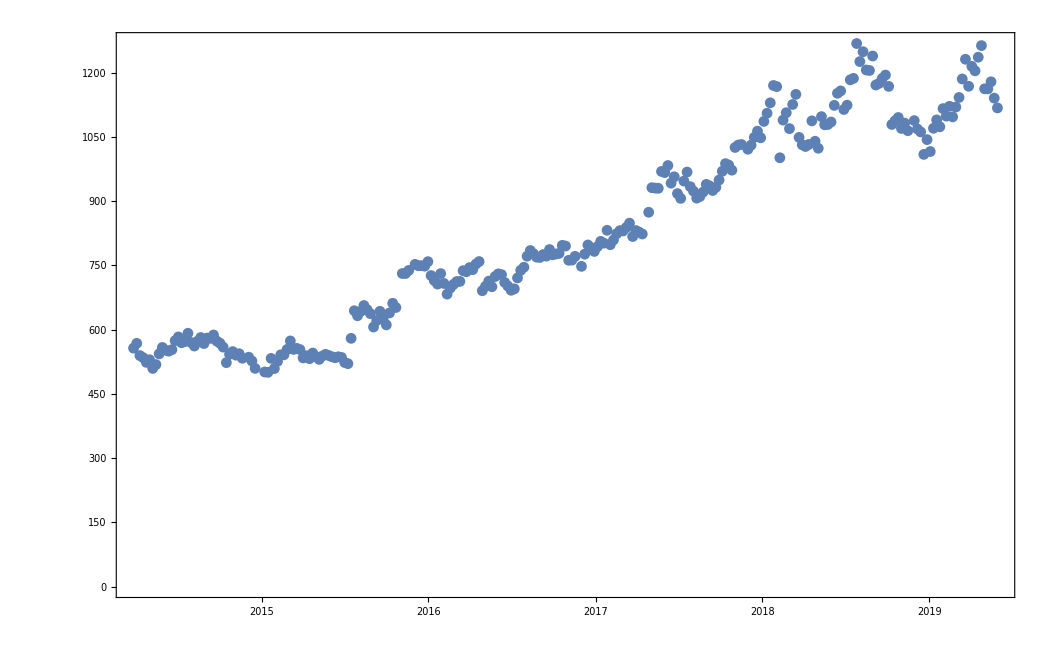

```mathematica
DateListPlot[
Out[24],
Joined->False,ColorFunction->"DarkRainbow"]
```

```mathematica
Map[Last,Out@24]
```

{556.93 $,568.18 $,539.47 $,534.63 $,523.72 $,529.90 $,509.60 $,518.56 $,543.57 $,558.55 $,552.38 $,549.84 $,553.38 $,574.42 $,583.13 $,569.54 $,572.16 $,591.73 $,570.03 $,561.82 $,573.08 $,581.77 $,567.64 $,580.39 $,579.76 $,587.66 $,573.49 $,568.52 $,559.34 $,523.07 $,542.49 $,548.80 $,540.56 $,543.89 $,533.37 $,535.84 $,526.89 $,509.70 $,501.30 $,500.42 $,532.93 $,509.26 $,526.14 $,541.44 $,541.38 $,553.96 $,573.76 $,553.99 $,556.46 $,553.65 $,534.06 $,539.30 $,532.34 $,545.50 $,537.34 $,530.70 $,538.40 $,542.51 $,539.78 $,536.70 $,534.61 $,536.73 $,535.23 $,523.40 $,520.68 $,579.85 $,644.28 $,632.59 $,642.68 $,656.45 $,646.83 $,637.61 $,606.25 $,621.35 $,642.90 $,625.80 $,611.29 $,639.16 $,661.74 $,651.79 $,731.25 $,731.23 $,738.41 $,752.54 $,749.46 $,749.43 $,748.40 $,758.88 $,726.39 $,714.72 $,706.59 $,730.96 $,708.01 $,683.11 $,697.35 $,705.75 $,712.42 $,712.82 $,737.78 $,735.30 $,744.95 $,740.28 $,753.20 $,759.14 $,691.02 $,701.43 $,713.31 $,700.32 $,724.12 $,730.40 $,728.58 $,710.36 $,701.87 $,692.10 $,695.36 $,720.95 $,738.63 $,745.91 $,771.61 $,784.85 $,777.50 $,769.41 $,768.78 $,775.32 $,771.76 $,787.21 $,775.01 $,776.86 $,778.19 $,796.97 $,795.35 $,762.13 $,762.56 $,771.23 $,747.92 $,776.42 $,797.85 $,791.26 $,782.79 $,794.02 $,806.36 $,802.17 $,832.15 $,798.53 $,809.56 $,824.16 $,831.33 $,830.63 $,838.68 $,848.78 $,817.58 $,831.50 $,827.88 $,823.56 $,874.25 $,931.66 $,930.60 $,930.24 $,969.54 $,966.95 $,983.41 $,942.31 $,957.09 $,917.79 $,906.69 $,947.16 $,968.15 $,934.09 $,923.65 $,907.24 $,910.98 $,921.28 $,939.33 $,935.95 $,925.11 $,932.45 $,949.50 $,969.96 $,987.83 $,984.45 $,972.56 $,1 025.58 $,1 031.26 $,1 032.50 $,1 021.41 $,1 030.93 $,1 049.15 $,1 063.63 $,1 048.14 $,1 086.40 $,1 105.52 $,1 129.79 $,1 170.37 $,1 167.70 $,1 001.52 $,1 089.52 $,1 106.63 $,1 069.52 $,1 126.00 $,1 149.58 $,1 049.08 $,1 031.79 $,1 027.81 $,1 032.51 $,1 087.70 $,1 040.04 $,1 023.72 $,1 097.57 $,1 078.59 $,1 079.24 $,1 084.99 $,1 123.86 $,1 152.12 $,1 157.66 $,1 114.22 $,1 124.27 $,1 183.48 $,1 186.96 $,1 268.33 $,1 226.15 $,1 249.10 $,1 206.49 $,1 205.38 $,1 239.12 $,1 171.44 $,1 175.33 $,1 186.87 $,1 194.64 $,1 168.19 $,1 079.32 $,1 087.97 $,1 095.57 $,1 070.00 $,1 082.40 $,1 064.71 $,1 088.30 $,1 068.73 $,1 061.90 $,1 009.41 $,1 043.88 $,1 016.06 $,1 070.33 $,1 089.90 $,1 073.90 $,1 116.37 $,1 098.71 $,1 121.67 $,1 096.97 $,1 119.92 $,1 142.32 $,1 185.55 $,1 231.54 $,1 168.49 $,1 215.00 $,1 204.62 $,1 236.37 $,1 263.45 $,1 162.61 $,1 162.38 $,1 178.98 $,1 140.77 $,1 117.95 $}

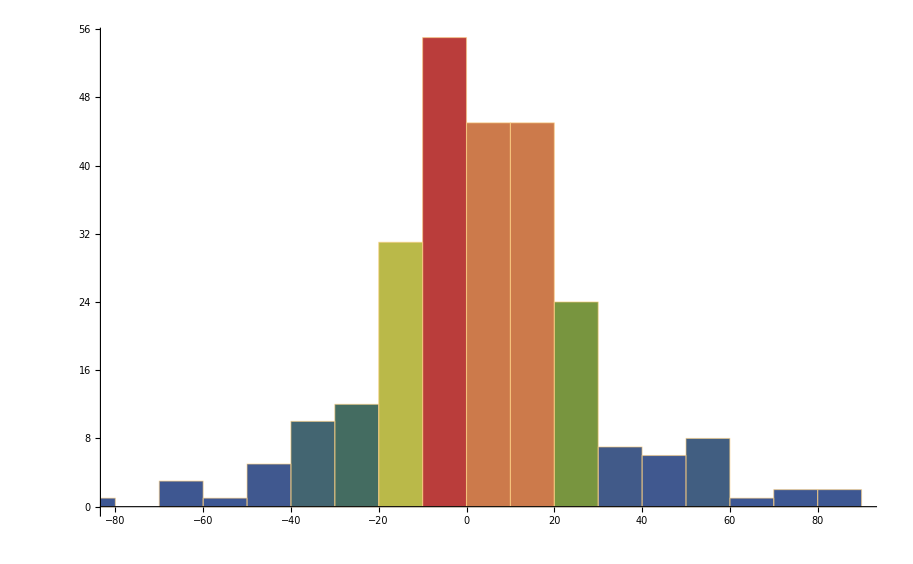

```mathematica
Histogram[
Differences@
Map[Last,Out@24],
ColorFunction->"DarkRainbow"]
```

```mathematica
Table[
Map[{#[[2]],Last[#]}&,Out[22][[i]]],
{i, 1, Length@Out[22]}]
```

{{{Thu 27 Mar 2014 00:00:00GMT-7.,556.93 $},{Thu 3 Apr 2014 00:00:00GMT-7.,568.18 $},{Thu 10 Apr 2014 00:00:00GMT-7.,539.47 $},{Thu 17 Apr 2014 00:00:00GMT-7.,534.63 $},255,{Thu 16 May 2019 00:00:00GMT-7.,1 178.98 $},{Thu 23 May 2019 00:00:00GMT-7.,1 140.77 $},{Thu 30 May 2019 00:00:00GMT-7.,1 117.95 $}},3,{1}}
 |  |  |  |

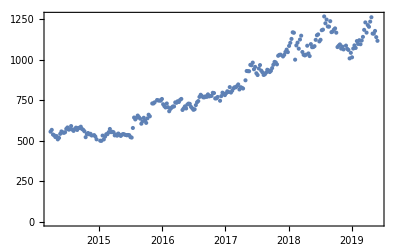
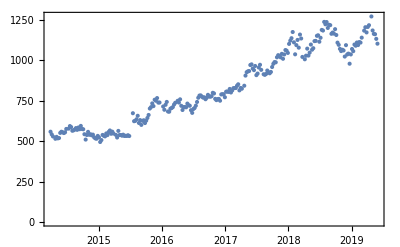
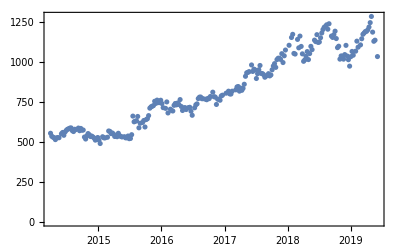
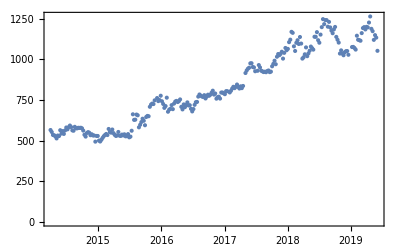
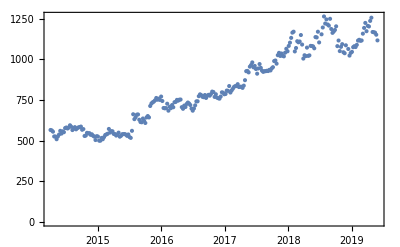

```mathematica
Table[
DateListPlot[
Map[{#[[2]],Last[#]}&,Out[22][[i]]],
Joined->False, ColorFunction->"DarkRainbow"
],{i, 1, Length@Out[22]}]
```

```mathematica
Length@Out@22
```

5

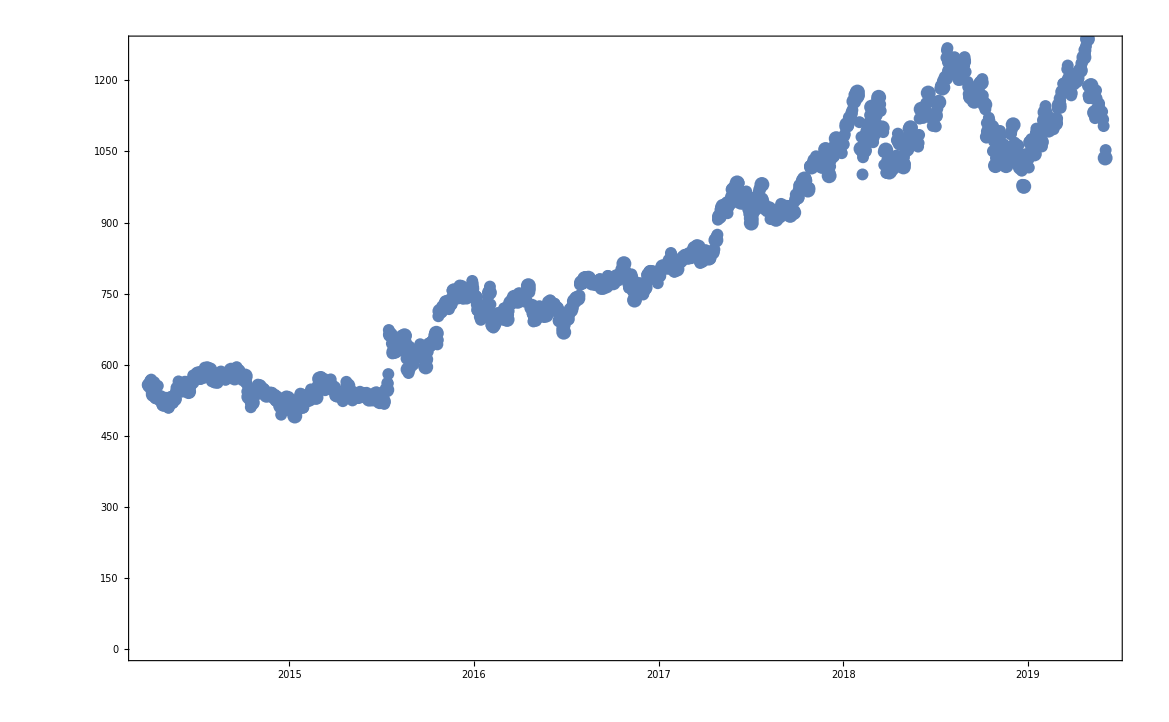

```mathematica
Show@Table[
DateListPlot[
Map[{#[[2]],Last[#]}&,Out[22][[i]]],
Joined->False, ColorFunction->"DarkRainbow"
],{i, 1, Length@Out[22]}]
```

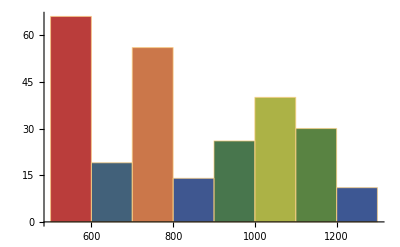
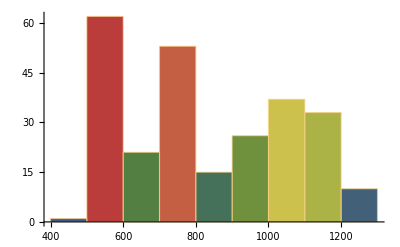
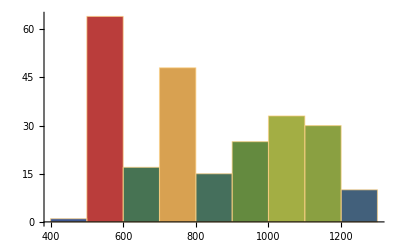
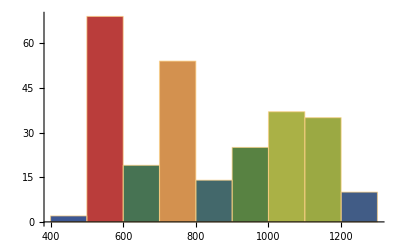
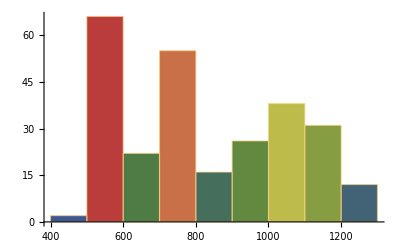

```mathematica
Table[
Histogram[
Map[Last,Out[22][[i]]],
ColorFunction->"DarkRainbow"],
{i, 1, Length@Out[22]}]
```

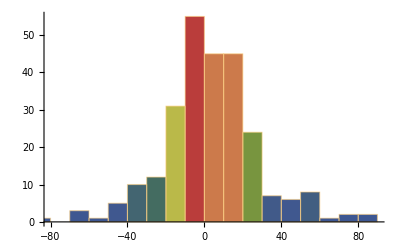
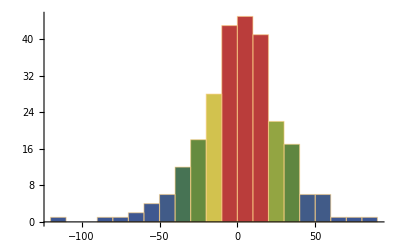
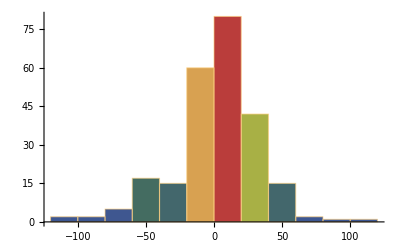
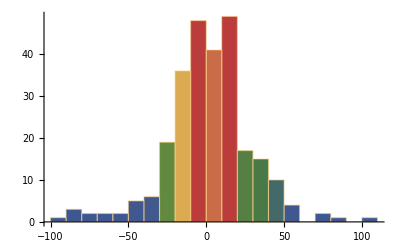
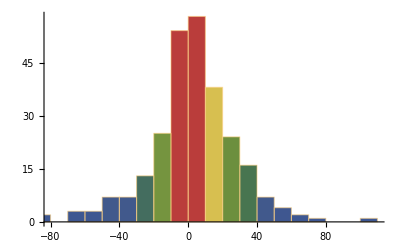

```mathematica
Table[
Histogram[
Differences@
Map[Last,Out[22][[i]]],
ColorFunction->"DarkRainbow"],
{i, 1, Length@Out[22]}]
```

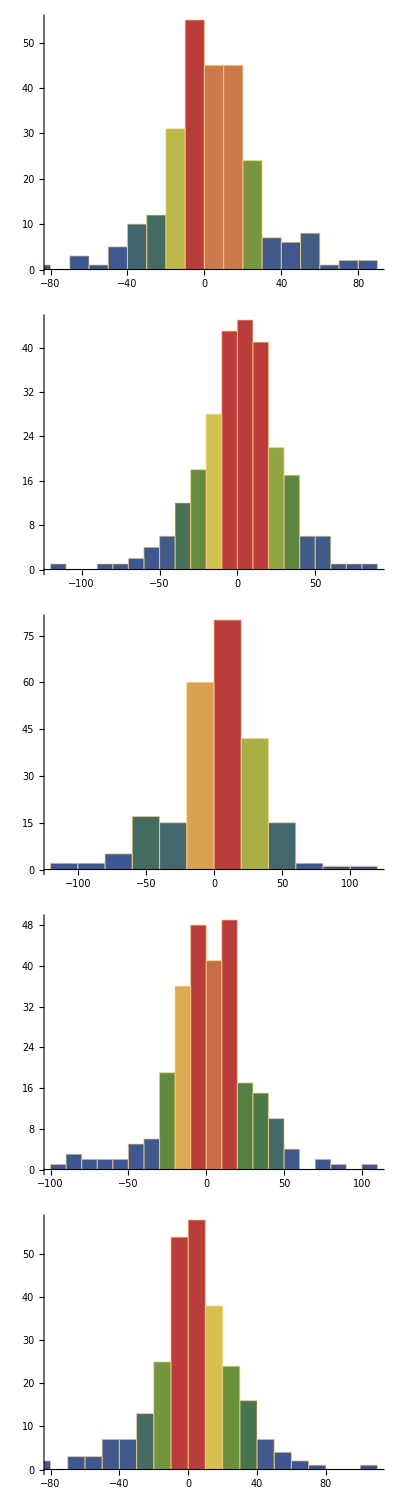

```mathematica
Column@
Table[
Histogram[
Differences@
Map[Last,Out[22][[i]]],
ColorFunction->"DarkRainbow"],
{i, 1, Length@Out[22]}]
```

```mathematica
Table[
Histogram[
Differences@
Map[Last,Out[22][[i]]],
ColorFunction->"DarkRainbow"],
{i, 1, Length@Out[22]}]
```

```mathematica
FinancialData["NASDAQ:AAPL", "Price", 2018]
```

FinancialData::notdate: 2018 is not a valid date range for FinancialData.

FinancialData[NASDAQ:AAPL,Price,2018]

```mathematica
FinancialData["NASDAQ:AAPL", "Price", {2018}]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
FinancialData["NASDAQ:AAPL", "Price", {2018}]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
FinancialData["NASDAQ:AAPL", "Price", All]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
FinancialData["NASDAQ:AAPL", "Price", {2018}]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

$Failed

```mathematica
DateObject@DateObject[{2014,3,27,0,0,0.},"Instant","Gregorian",-7.]
```

Thu 27 Mar 2014 00:00:00GMT-7.

```mathematica
DateValue[DateObject[{2014,3,27,0,0,0.},"Instant","Gregorian",-7.],"DayName"]
```

Thursday

```mathematica
DayName@DateObject[{2014,3,27,0,0,0.},"Instant","Gregorian",-7.]
```

Thursday

```mathematica
DayName@DateObject[{2014,3,27,0,0,0.},"Instant","Gregorian",-7.]
```

Thursday

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DayName@#&]
]
```

DayName::date: Expression {DateObject[{1997,5,15,0,0,0.},Instant,Gregorian,-7.],1.96} cannot be interpreted as a date specification.

DayName::date: Expression {DateObject[{1997,5,16,0,0,0.},Instant,Gregorian,-7.],1.73} cannot be interpreted as a date specification.

DayName::date: Expression {DateObject[{1997,5,19,0,0,0.},Instant,Gregorian,-7.],1.71} cannot be interpreted as a date specification.

General::stop: Further output of DayName::date will be suppressed during this calculation.

{{{Thu 15 May 1997 00:00:00GMT-7.,1.96 $}},{{Fri 16 May 1997 00:00:00GMT-7.,1.73 $}},{{Mon 19 May 1997 00:00:00GMT-7.,1.71 $}},{{Tue 20 May 1997 00:00:00GMT-7.,1.64 $}},5544,{{Mon 3 Jun 2019 00:00:00GMT-7.,1 692.69 $}},{{Tue 4 Jun 2019 00:00:00GMT-7.,1 729.56 $}},{{Wed 5 Jun 2019 00:00:00GMT-7.,1 738.50 $}}}
 |  |  |  |

```mathematica
Length@Out[45]
```

5551

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DayName@DateObject@#&]
]
```

DayName::date: Expression DateObject[{DateObject[{1997,5,15,0,0,0.},Instant,Gregorian,-7.],1.96}] cannot be interpreted as a date specification.

DayName::date: Expression DateObject[{DateObject[{1997,5,16,0,0,0.},Instant,Gregorian,-7.],1.73}] cannot be interpreted as a date specification.

DayName::date: Expression DateObject[{DateObject[{1997,5,19,0,0,0.},Instant,Gregorian,-7.],1.71}] cannot be interpreted as a date specification.

General::stop: Further output of DayName::date will be suppressed during this calculation.

{{{Thu 15 May 1997 00:00:00GMT-7.,1.96 $}},{{Fri 16 May 1997 00:00:00GMT-7.,1.73 $}},{{Mon 19 May 1997 00:00:00GMT-7.,1.71 $}},{{Tue 20 May 1997 00:00:00GMT-7.,1.64 $}},5544,{{Mon 3 Jun 2019 00:00:00GMT-7.,1 692.69 $}},{{Tue 4 Jun 2019 00:00:00GMT-7.,1 729.56 $}},{{Wed 5 Jun 2019 00:00:00GMT-7.,1 738.50 $}}}
 |  |  |  |

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DateValue[DateObject[#,"Instant","Gregorian",-7.],"DayName"]&]
]
```

DateValue::arg: Argument DateObject[{DateObject[{1997,5,15,0,0,0.},Instant,Gregorian,-7.],1.96},Instant,CalendarType→Gregorian,TimeZone→-7.,DateFormat→Automatic] cannot be interpreted as a date or time input

DateValue::arg: Argument DateObject[{DateObject[{1997,5,16,0,0,0.},Instant,Gregorian,-7.],1.73},Instant,CalendarType→Gregorian,TimeZone→-7.,DateFormat→Automatic] cannot be interpreted as a date or time input

DateValue::arg: Argument DateObject[{DateObject[{1997,5,19,0,0,0.},Instant,Gregorian,-7.],1.71},Instant,CalendarType→Gregorian,TimeZone→-7.,DateFormat→Automatic] cannot be interpreted as a date or time input

General::stop: Further output of DateValue::arg will be suppressed during this calculation.

{{{Thu 15 May 1997 00:00:00GMT-7.,1.96 $}},{{Fri 16 May 1997 00:00:00GMT-7.,1.73 $}},{{Mon 19 May 1997 00:00:00GMT-7.,1.71 $}},{{Tue 20 May 1997 00:00:00GMT-7.,1.64 $}},5544,{{Mon 3 Jun 2019 00:00:00GMT-7.,1 692.69 $}},{{Tue 4 Jun 2019 00:00:00GMT-7.,1 729.56 $}},{{Wed 5 Jun 2019 00:00:00GMT-7.,1 738.50 $}}}
 |  |  |  |

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DayName@First@#&]
]
```

{{{Thu 15 May 1997 00:00:00GMT-7.,1.96 $},{Thu 22 May 1997 00:00:00GMT-7.,1.40 $},{Thu 29 May 1997 00:00:00GMT-7.,1.51 $},{Thu 5 Jun 1997 00:00:00GMT-7.,1.54 $},1111,{Thu 16 May 2019 00:00:00GMT-7.,1 907.57 $},{Thu 23 May 2019 00:00:00GMT-7.,1 815.48 $},{Thu 30 May 2019 00:00:00GMT-7.,1 816.32 $}},3,{1}}
 |  |  |  |

```mathematica
Length@Out@49
```

5

```mathematica
Table[
Histogram[
Differences@
Map[Last,Out[22][[i]]],
ColorFunction->"DarkRainbow"],
{i, 1, Length@Out[22]}]
```

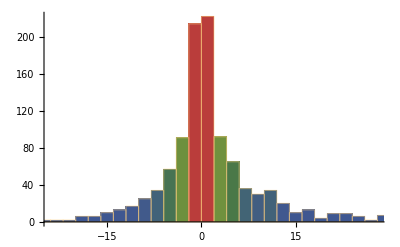
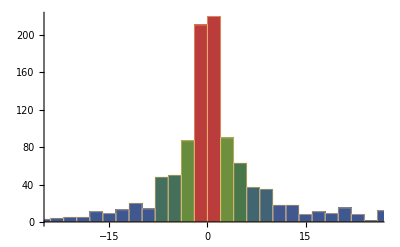
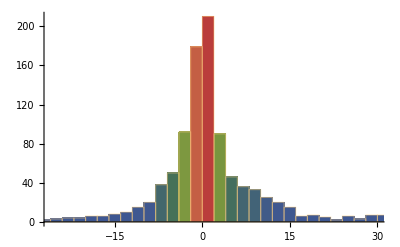
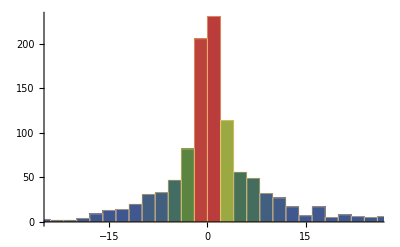
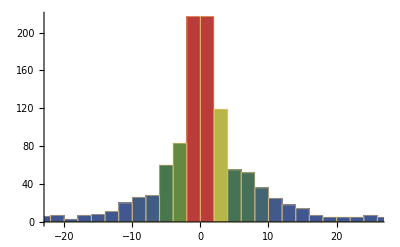

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
With[{days=GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DayName@First@#&]},
Table[
Histogram[
Differences@
Map[Last,days[[i]]],
ColorFunction->"DarkRainbow"],
{i, 1, 5}]
]]
```

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
With[{days=GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DayName@First@#&]},
Table[
Differences@
Map[Last,days[[i]]],
{i, 1, 5}]
]]
```

{1}
 |  |  |  |

```mathematica
Length@Out@53
```

5

```mathematica
Table[
With[{
values=Out[53][[i]],
lessthan=Select[Out[53][[i]], #<0&],
greaterthan=Select[Out[53][[i]], #<0&]},
{Total@values, Total@lessthan,Total@greaterthan}
], {i, 1, 5}]
```

{{1 814.36 $,0,0},{1 773.34 $,0,0},{1 690.98 $,0,0},{1 727.92 $,0,0},{1 737.07 $,0,0}}

```mathematica
Table[
With[{
values=Differences@Out[53][[i]],
lessthan=Select[Out[53][[i]], #<0&],
greaterthan=Select[Out[53][[i]], #<0&]},
{Total@values, Total@lessthan,Total@greaterthan}
], {i, 1, 5}]
```

{{1.40 $,0,0},{-47.98 $,0,0},{-166.08 $,0,0},{-106.82 $,0,0},{-80.79 $,0,0}}

```mathematica
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], #<0&]},
{Total@values, Total@lessthan,Total@greaterthan}
]], {i, 1, 5}]
```

{{1.40 $,-4 078.28 $,0},{-47.98 $,-4 272.52 $,0},{-166.08 $,-4 663.13 $,0},{-106.82 $,-4 348.27 $,0},{-80.79 $,-4 357.62 $,0}}

```mathematica
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#<0&]},
{Total@values, Total@lessthan,Total@greaterthan}
]], {i, 1, 5}]
```

{{1.40 $,-4 078.28 $,-4 078.28 $},{-47.98 $,-4 272.52 $,-4 272.52 $},{-166.08 $,-4 663.13 $,-4 663.13 $},{-106.82 $,-4 348.27 $,-4 348.27 $},{-80.79 $,-4 357.62 $,-4 357.62 $}}

```mathematica
Grid@
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#<0&]},
{Total@values, Total@lessthan,Total@greaterthan}
]], {i, 1, 5}]
```

1.40 $ | -4 078.28 $ | -4 078.28 $
-47.98 $ | -4 272.52 $ | -4 272.52 $
-166.08 $ | -4 663.13 $ | -4 663.13 $
-106.82 $ | -4 348.27 $ | -4 348.27 $
-80.79 $ | -4 357.62 $ | -4 357.62 $

```mathematica
Grid@
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#>0&]},
{Total@values, Total@lessthan,Total@greaterthan}
]], {i, 1, 5}]
```

1.40 $ | -4 078.28 $ | 5 892.64 $
-47.98 $ | -4 272.52 $ | 6 045.86 $
-166.08 $ | -4 663.13 $ | 6 354.11 $
-106.82 $ | -4 348.27 $ | 6 076.19 $
-80.79 $ | -4 357.62 $ | 6 094.69 $

```mathematica
Grid@
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#>0&]},
{Total@values, Total@lessthan,Total@greaterthan,Total@greaterthan-Total@lessthan}
]], {i, 1, 5}]
```

1.40 $ | -4 078.28 $ | 5 892.64 $ | 9 970.92 $
-47.98 $ | -4 272.52 $ | 6 045.86 $ | 10 318.38 $
-166.08 $ | -4 663.13 $ | 6 354.11 $ | 11 017.24 $
-106.82 $ | -4 348.27 $ | 6 076.19 $ | 10 424.46 $
-80.79 $ | -4 357.62 $ | 6 094.69 $ | 10 452.31 $

```mathematica
Grid@
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#>0&]},
{Total@values, Total@lessthan,Total@greaterthan,Total@greaterthan+Total@lessthan}
]], {i, 1, 5}]
```

1.40 $ | -4 078.28 $ | 5 892.64 $ | 1 814.36 $
-47.98 $ | -4 272.52 $ | 6 045.86 $ | 1 773.34 $
-166.08 $ | -4 663.13 $ | 6 354.11 $ | 1 690.98 $
-106.82 $ | -4 348.27 $ | 6 076.19 $ | 1 727.92 $
-80.79 $ | -4 357.62 $ | 6 094.69 $ | 1 737.07 $

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
With[{days=GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DayName@First@#&]},
Table[
Histogram[
Differences@
Map[Last,days[[i]]],
ColorFunction->"DarkRainbow"],
{i, 1, 5}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Grid@
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#>0&]},
{Total@values, Total@lessthan,Total@greaterthan,Total@greaterthan+Total@lessthan}
]], {i, 1, 5}]
```

```mathematica
Grid@
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#>0&]},{
Total@values,
 Total@lessthan,
Total@greaterthan,
Total@greaterthan+Total@lessthan,
Mean@values,
Variance@values,
Min@values,
Max@values,
Kurtosis@values,
Skewness@values
}]], {i, 1, 5}]
```

1.40 $ | -4 078.28 $ | 5 892.64 $ | 1 814.36 $ | 0.00 $ | 856.259 $^2 | -224.85 $ | 241.42 $ | 23.5766 | 0.223355
-47.98 $ | -4 272.52 $ | 6 045.86 $ | 1 773.34 $ | -0.04 $ | 836.23 $^2 | -249.15 $ | 315.03 $ | 37.6649 | 1.07269
-166.08 $ | -4 663.13 $ | 6 354.11 $ | 1 690.98 $ | -0.16 $ | 1303.27 $^2 | -322.36 $ | 339.34 $ | 33.7844 | 0.450638
-106.82 $ | -4 348.27 $ | 6 076.19 $ | 1 727.92 $ | -0.09 $ | 803.023 $^2 | -187.02 $ | 350.67 $ | 36.4281 | 2.09455
-80.79 $ | -4 357.62 $ | 6 094.69 $ | 1 737.07 $ | -0.07 $ | 951.998 $^2 | -313.96 $ | 273.99 $ | 34.2059 | -0.0976809

```mathematica
Grid@
Join[{"Sum", "Less than 0", "Greater than 0", "Diff", "Mean", "Variance", "Min", "Max", "Kurtosis", "Skewness"},
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#>0&]},{
Total@values,
 Total@lessthan,
Total@greaterthan,
Total@greaterthan+Total@lessthan,
Mean@values,
Variance@values,
Min@values,
Max@values,
Kurtosis@values,
Skewness@values
}]], {i, 1, 5}]]
```

Grid[{Sum,Less than 0,Greater than 0,Diff,Mean,Variance,Min,Max,Kurtosis,Skewness,{1.40 $,-4 078.28 $,5 892.64 $,1 814.36 $,0.00 $,856.259 $^2,-224.85 $,241.42 $,23.5766,0.223355},{-47.98 $,-4 272.52 $,6 045.86 $,1 773.34 $,-0.04 $,836.23 $^2,-249.15 $,315.03 $,37.6649,1.07269},{-166.08 $,-4 663.13 $,6 354.11 $,1 690.98 $,-0.16 $,1303.27 $^2,-322.36 $,339.34 $,33.7844,0.450638},{-106.82 $,-4 348.27 $,6 076.19 $,1 727.92 $,-0.09 $,803.023 $^2,-187.02 $,350.67 $,36.4281,2.09455},{-80.79 $,-4 357.62 $,6 094.69 $,1 737.07 $,-0.07 $,951.998 $^2,-313.96 $,273.99 $,34.2059,-0.0976809}}]

```mathematica
Join[{{"Sum", "Less than 0", "Greater than 0", "Diff", "Mean", "Variance", "Min", "Max", "Kurtosis", "Skewness"}},
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#>0&]},{
Total@values,
 Total@lessthan,
Total@greaterthan,
Total@greaterthan+Total@lessthan,
Mean@values,
Variance@values,
Min@values,
Max@values,
Kurtosis@values,
Skewness@values
}]], {i, 1, 5}]]
```

{{Sum,Less than 0,Greater than 0,Diff,Mean,Variance,Min,Max,Kurtosis,Skewness},{1.40 $,-4 078.28 $,5 892.64 $,1 814.36 $,0.00 $,856.259 $^2,-224.85 $,241.42 $,23.5766,0.223355},{-47.98 $,-4 272.52 $,6 045.86 $,1 773.34 $,-0.04 $,836.23 $^2,-249.15 $,315.03 $,37.6649,1.07269},{-166.08 $,-4 663.13 $,6 354.11 $,1 690.98 $,-0.16 $,1303.27 $^2,-322.36 $,339.34 $,33.7844,0.450638},{-106.82 $,-4 348.27 $,6 076.19 $,1 727.92 $,-0.09 $,803.023 $^2,-187.02 $,350.67 $,36.4281,2.09455},{-80.79 $,-4 357.62 $,6 094.69 $,1 737.07 $,-0.07 $,951.998 $^2,-313.96 $,273.99 $,34.2059,-0.0976809}}

```mathematica
Grid@
Join[{{"Sum", "Less than 0", "Greater than 0", "Diff", "Mean", "Variance", "Min", "Max", "Kurtosis", "Skewness"}},
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#>0&]},{
Total@values,
 Total@lessthan,
Total@greaterthan,
Total@greaterthan+Total@lessthan,
Mean@values,
Variance@values,
Min@values,
Max@values,
Kurtosis@values,
Skewness@values
}]], {i, 1, 5}]]
```

Sum | Less than 0 | Greater than 0 | Diff | Mean | Variance | Min | Max | Kurtosis | Skewness
1.40 $ | -4 078.28 $ | 5 892.64 $ | 1 814.36 $ | 0.00 $ | 856.259 $^2 | -224.85 $ | 241.42 $ | 23.5766 | 0.223355
-47.98 $ | -4 272.52 $ | 6 045.86 $ | 1 773.34 $ | -0.04 $ | 836.23 $^2 | -249.15 $ | 315.03 $ | 37.6649 | 1.07269
-166.08 $ | -4 663.13 $ | 6 354.11 $ | 1 690.98 $ | -0.16 $ | 1303.27 $^2 | -322.36 $ | 339.34 $ | 33.7844 | 0.450638
-106.82 $ | -4 348.27 $ | 6 076.19 $ | 1 727.92 $ | -0.09 $ | 803.023 $^2 | -187.02 $ | 350.67 $ | 36.4281 | 2.09455
-80.79 $ | -4 357.62 $ | 6 094.69 $ | 1 737.07 $ | -0.07 $ | 951.998 $^2 | -313.96 $ | 273.99 $ | 34.2059 | -0.0976809

```mathematica
Grid@
Join[{{"Sum", "Less than 0", "Greater than 0", "Diff", "Mean", "Variance", "Min", "Max", "Median", "Kurtosis", "Skewness"}},
Table[
With[{
values=Differences@Out[53][[i]]
},With[{
lessthan=Select[Out[53][[i]], QuantityMagnitude@#<0&],
greaterthan=Select[Out[53][[i]], QuantityMagnitude@#>0&]},{
Total@values,
 Total@lessthan,
Total@greaterthan,
Total@greaterthan+Total@lessthan,
Mean@values,
Variance@values,
Min@values,
Max@values,
Median@values,
Kurtosis@values,
Skewness@values
}]], {i, 1, 5}]]
```

Sum | Less than 0 | Greater than 0 | Diff | Mean | Variance | Min | Max | Median | Kurtosis | Skewness
1.40 $ | -4 078.28 $ | 5 892.64 $ | 1 814.36 $ | 0.00 $ | 856.259 $^2 | -224.85 $ | 241.42 $ | -0.08 $ | 23.5766 | 0.223355
-47.98 $ | -4 272.52 $ | 6 045.86 $ | 1 773.34 $ | -0.04 $ | 836.23 $^2 | -249.15 $ | 315.03 $ | 0.14 $ | 37.6649 | 1.07269
-166.08 $ | -4 663.13 $ | 6 354.11 $ | 1 690.98 $ | -0.16 $ | 1303.27 $^2 | -322.36 $ | 339.34 $ | 0.06 $ | 33.7844 | 0.450638
-106.82 $ | -4 348.27 $ | 6 076.19 $ | 1 727.92 $ | -0.09 $ | 803.023 $^2 | -187.02 $ | 350.67 $ | -0.08 $ | 36.4281 | 2.09455
-80.79 $ | -4 357.62 $ | 6 094.69 $ | 1 737.07 $ | -0.07 $ | 951.998 $^2 | -313.96 $ | 273.99 $ | 0.04 $ | 34.2059 | -0.0976809

```mathematica
Grid@
With[{ops={Sum, Mean, Variance, Min, Max, Median, Kurtosis, Skewness}},
Join[{ops},
Table[
With[{values=Differences@Out[53][[i]]},
Map[#[values]&,ops]], {i, 1, 5}]]]
```

Sum::argmu: Sum called with 1 argument; 2 or more arguments are expected.

General::stop: Further output of Sum::argmu will be suppressed during this calculation.

1
 |  |  |  |

```mathematica
Grid@
With[{ops={Total, Mean, Variance, Min, Max, Median, Kurtosis, Skewness}},
Join[{ops},
Table[
Map[#[Differences@Out[53][[i]]]&,ops], {i, 1, 5}]]]
```

Total | Mean | Variance | Min | Max | Median | Kurtosis | Skewness
1.40 $ | 0.00 $ | 856.259 $^2 | -224.85 $ | 241.42 $ | -0.08 $ | 23.5766 | 0.223355
-47.98 $ | -0.04 $ | 836.23 $^2 | -249.15 $ | 315.03 $ | 0.14 $ | 37.6649 | 1.07269
-166.08 $ | -0.16 $ | 1303.27 $^2 | -322.36 $ | 339.34 $ | 0.06 $ | 33.7844 | 0.450638
-106.82 $ | -0.09 $ | 803.023 $^2 | -187.02 $ | 350.67 $ | -0.08 $ | 36.4281 | 2.09455
-80.79 $ | -0.07 $ | 951.998 $^2 | -313.96 $ | 273.99 $ | 0.04 $ | 34.2059 | -0.0976809

```mathematica
Grid@
With[{ops={Total, Mean, Variance, Min,Max@#-Abs@Min@#&, Max, Median, Kurtosis, Skewness}},
Join[{ops},
Table[
Map[#[Differences@Out[53][[i]]]&,ops], {i, 1, 5}]]]
```

Total | Mean | Variance | Min | Max[#1]-Abs[Min[#1]]& | Max | Median | Kurtosis | Skewness
1.40 $ | 0.00 $ | 856.259 $^2 | -224.85 $ | 16.57 $ | 241.42 $ | -0.08 $ | 23.5766 | 0.223355
-47.98 $ | -0.04 $ | 836.23 $^2 | -249.15 $ | 65.88 $ | 315.03 $ | 0.14 $ | 37.6649 | 1.07269
-166.08 $ | -0.16 $ | 1303.27 $^2 | -322.36 $ | 16.98 $ | 339.34 $ | 0.06 $ | 33.7844 | 0.450638
-106.82 $ | -0.09 $ | 803.023 $^2 | -187.02 $ | 163.65 $ | 350.67 $ | -0.08 $ | 36.4281 | 2.09455
-80.79 $ | -0.07 $ | 951.998 $^2 | -313.96 $ | -39.97 $ | 273.99 $ | 0.04 $ | 34.2059 | -0.0976809

```mathematica
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
With[{days=GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DayName@First@#&]},
Table[
Histogram[
Differences@
Map[Last,days[[i]]],
ColorFunction->"DarkRainbow"],
{i, 1, 5}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}



```mathematica
Plot[x^2,{x,-2,2}]
```

```mathematica
1/2==∫_0^a x^2 ⅆx
```

1/2==a^3/3

```mathematica
FindInstance[1/2==a^3/3,{a}]
```

{{a→Root1.14Root[-3+2 #1^3&,1]1.1447142425533319}}

```mathematica
Reduce[1/2==a^3/3]
```

a==-(-3/2)^(1/3)||a==(3/2)^(1/3)||a==(-1)^(2/3) (3/2)^(1/3)

```mathematica
Solve[a==-(-3/2)^(1/3)||a==(3/2)^(1/3)||a==(-1)^(2/3) (3/2)^(1/3),{a}]
```

{{a→-(-3/2)^(1/3)},{a→(3/2)^(1/3)},{a→(-1)^(2/3) (3/2)^(1/3)}}

```mathematica
{(-3/2)^(1/3),(3/2)^(1/3),(-1)^(2/3) (3/2)^(1/3)}
```

{(-3/2)^(1/3),(3/2)^(1/3),(-1)^(2/3) (3/2)^(1/3)}

```mathematica
N@{(-3/2)^(1/3),(3/2)^(1/3),(-1)^(2/3) (3/2)^(1/3)}
```

{0.572357+0.991352 ⅈ,1.14471,-0.572357+0.991352 ⅈ}

```mathematica
Integrate[x^2,{x,0,(3/2)^(1/3)}]
```

1/2

```mathematica
Integrate[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}]
```

1

```mathematica
ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}]
```

ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}]

```mathematica
Moment[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}],4]
```

9/14 (3/2)^(1/3)

```mathematica
Moment[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}],3]
```

0

```mathematica
Moment[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}],2]
```

3/5 (3/2)^(2/3)

```mathematica
Moment[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}],1]
```

0

```mathematica
Kurtosis[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}]]
```

25/21

```mathematica
N[25/21]
```

1.19048

```mathematica
Skewness[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}]]
```

0

```mathematica
Variance[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}]]
```

3/5 (3/2)^(2/3)

```mathematica
StandardDeviation[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}]]
```

3^(5/6)/(2^(1/3) √5)

```mathematica
N[3^(5/6)/(2^(1/3) √5)]
```

0.886692

```mathematica
Mean[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}]]
```

0

```mathematica
CDF[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}],x]
```

Piecewise[{{1, x>(3/2)^(1/3)}, {1/6 (3+2 x^3), -(3/2)^(1/3)<x≤(3/2)^(1/3)}, {0, True}}]

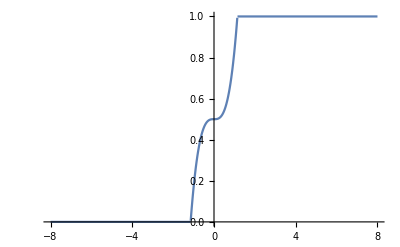

```mathematica
Plot[Piecewise[{{1,x>(3/2)^(1/3)},{1/6 (3+2 x^3),-(3/2)^(1/3)<x≤(3/2)^(1/3)}},0],{x,-8,8}]
```

```mathematica
PDF[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}],x]
```

Piecewise[{{x^2, -(3/2)^(1/3)<x<(3/2)^(1/3)}, {0, True}}]

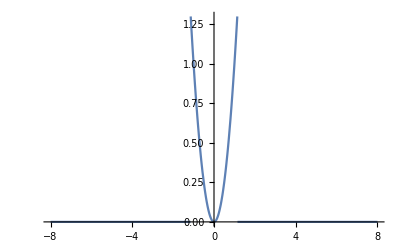

```mathematica
Plot[Piecewise[{{x^2,-(3/2)^(1/3)<x<(3/2)^(1/3)}},0],{x,-8,8}]
```

```mathematica
ProbabilityDistribution[0,{x,0,0}]
```

ProbabilityDistribution[0,{x,0,0}]

```mathematica
Kurtosis[ProbabilityDistribution[0,{x,0,0}]]
```

Kurtosis[ProbabilityDistribution[0,{x,0,0}]]

```mathematica
Skewness[ProbabilityDistribution[0,{x,0,0}]]
```

Skewness[ProbabilityDistribution[0,{x,0,0}]]

```mathematica
RandomVariate[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}],10]
```

{0.684751,-0.525469,-1.1308,-0.640316,-0.788433,0.729447,0.738026,0.870788,-1.02978,-0.924131}

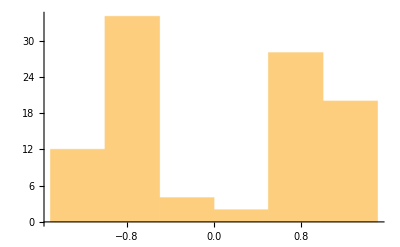

```mathematica
Histogram@
RandomVariate[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}],100]
```

```mathematica
|
```

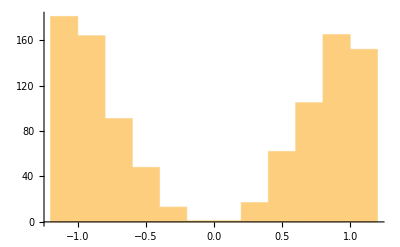

```mathematica
Histogram@
RandomVariate[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}],1000]
```

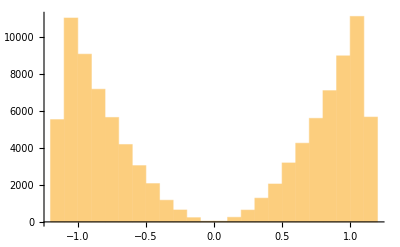

```mathematica
Histogram@
RandomVariate[ProbabilityDistribution[x^2,{x,-(3/2)^(1/3),(3/2)^(1/3)}],100000]
```



```mathematica
Plot[Sin[x],{x,0,2π}]
```

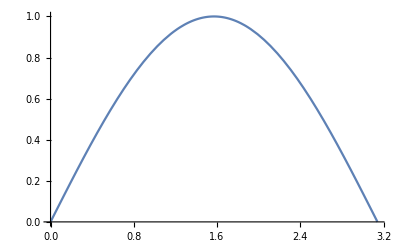

```mathematica
Plot[Sin[x],{x,0,π}]
```

```mathematica
Integrate[Sin[x],{x,0,π}]
```

2

```mathematica
Integrate[Sin[x],{x,0,π}]
```

2

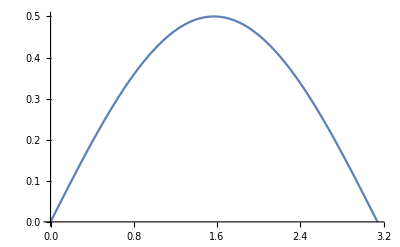

```mathematica
Plot[Sin[x]/2,{x,0,π}]
```

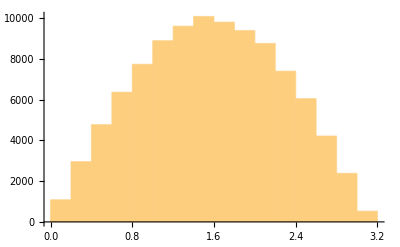

```mathematica
Histogram@
RandomVariate[ProbabilityDistribution[Sin[x]/2,{x,0,π}],100000]
```

```mathematica
TransformedDistribution[2 u+b,u\[Distributed]NormalDistribution[μ,σ]]
```

NormalDistribution[b+2 μ,2 σ]

```mathematica
TransformedDistribution[u u,u\[Distributed]NormalDistribution[μ,σ]]
```

TransformedDistribution[x^2,x\[Distributed]NormalDistribution[μ,σ]]

```mathematica
PDF[TransformedDistribution[x^2,x\[Distributed]NormalDistribution[μ,σ]],x]
```

Piecewise[{{(ⅇ^(-(√x+μ)^2/(2 σ^2)) (1+ⅇ^((2 √x μ)/σ^2)))/(2 √(2 π) √x σ), x>0}, {0, x<0}, {Indeterminate, True}}]

```mathematica
Manipulate[Plot[Piecewise[{{(ⅇ^(-(√x+μ)^2/(2 σ^2)) (1+ⅇ^((2 √x μ)/σ^2)))/(2 √(2 π) √x σ),x>0},{0,x<0}},Indeterminate],{x,-8,8}],{μ,-8,8},{σ,-2,2}]
```

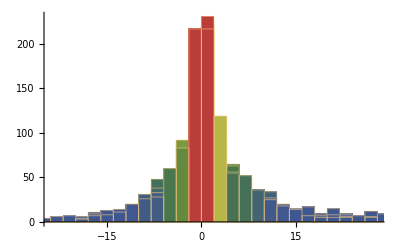

```mathematica
Show@
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
With[{days=GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DayName@First@#&]},
Table[
Histogram[
Differences@
Map[Last,days[[i]]],
ColorFunction->"DarkRainbow"],
{i, 1, 5}]]]
```

```mathematica
Show@
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
With[{days=GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DayName@First@#&]},
Table[
Histogram[
Differences@
Map[Last,days[[i]]],
ColorFunction->"DarkRainbow"],
{i, 1, 5}]]]
```

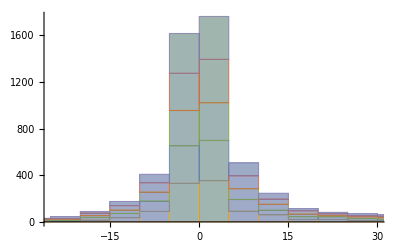

```mathematica
Histogram[
With[{list=FinancialData["NASDAQ:AMZN", "Price", All]},
With[{days=GatherBy[
Transpose[{
list["Dates"],
list["Values"]
}], DayName@First@#&]},
Table[
Differences@
Map[Last,days[[i]]],
{i, 1, 5}]]],
ColorFunction->"DarkRainbow", ChartLayout->"Stacked"]
```